# Full Calcium Signaling Model_Parameter Build Up 10

This notebook builds off of the LR Model with Calcium Model_Tissue_Full_Simplified_06 notebook and singleCellScaleTest notebook. The goal is to build up a parameter set for the model that reproduces experimental data. The workflow is outlined in the “Parameter Protocol” word document.

Version 02 put into each model version running a single-cell unwounded model to obtain initial conditions given a parameter set. This way, for example, if a parameter set would drain the ER before wounding then this is actually what the model would start with rather than starting with a “full” ER upon wounding.

Version 03 tries a bidirectional model of SERCA

J_SERCA=η_SERCA*(c^2-k1^2 k2^2 cER^2)/(c^2+k1^2)

Version 04 adds the Hill coefficient for the NCX Hill Function to be something other than 1. This is to try and let the NCX cut off at a smaller calcium level, thus giving a first expansion that decays more slowly as well as less PM interference with the second expansion

Version 05 adds in the high damage region with a longer healing time constant to replicate cells with high damage as well as looking at randomizing tissue parameters to break up radial symmetry.
Update high damage to be based on nuclear membrane damage zone predicted by O’Connor et al using initial calcium radius.
Update some damage specifications that were repeated between the initialization section and the final model section.

Version 05_02 looks at connection to the ablated region rather than microtears that are longer to heal with a high-damage region. Testing will involve putting equilibrium calcium being 1-2 cell rings past the ablated region post-wounding. Also modify random cell-cell variation to pull from absolute value of normal distribution rather than resampling negative values. For μ=1. and σ=.5 the latter is not much different from a true normal distribution.

Version 06 adds in wound size scaling. This is just an option for the full model for testing / sweeping in ACCRE, not for parameter testing on computer. Wound size scaling scales
1) The variables in the LR model that relate to wound size (see O’Connor et. al. for more details)
2) The radius of the ablated region and cavitation bubble
3) The horizontal stretch/compression of the μT distribution function (should be fixed already from #2 above)
4) The maximum μT conductance (?)

Version 07 adds in initial GBP scaling to mimic starvation experiments. Like wound scaling, this should just be an option for ACCRE scaling.

Version 08 changes the ACCRE model so that the random parameter variation is pulled from a lognormal distribution whose mean is always 1. This is to avoid negative values in the multiplier.
Seems like for normal σ=.1 we want for log normal μ=-(.1)^2/2 and σ=.1, and for σ=.5 we want μ=-(.4)^2/2 and σ=.4

Version 09 changes the ACCRE model so that random parameter variation (except for GCaMP and GapJunctions) is pulled from a lognormal distribution whose mean is 1 and whose variance is .225. It also implements the ability to vary any parameter across the tissue. This is mostly for testing purposes right now, but a permanent set of parameters to vary across the tissue could be implemented in the future based on these tests.
Also add in jump the gap section for James’s defense.

Version 10 saves the final 10 frames of finding equilibrium position and then uses them for the frames before wounding. This is so we can pick up on any oscillating cells. I have also tried lowering the tLong value, since when cells were oscillating it was taking up a lot of memory in ACCRE.

Version 11 looks at a different control video to compare the first and second expansion to. Also use a wound scaled version of previous notebooks to match (scaled like in O’Connor et al 2021, wound scaled down 10%)

# Initializations

Just some things that are common throughout multiple steps

## Parameters

```mathematica
(*Parameters that will be varied*)
extParams={rμT,τHeal,rPMCA,kPMCA,rSOC,ηNCX,nNCX,kNCX,rlkPM,α,α0,kl,nl,Kc,ηIPR,ηSERCA,kSERCA1,kSERCA2,ηlkER,Bx,ηGJIP3,ηGJc,connectAblated};
```

```mathematica
(*Parameters that will not be varied*)
intParams=
{
kdeg->1.25 (*s^-1*),
(*δ->1.234*10^-3 (*dimensionless; one of 3 options given by Lemon (also rr)*),*)
ν->4.3*10^-9*15*10^-5 (*dm^3;Assumes a circular cell surface of 4.3*10^-9 dm^2 cell height of 15 μm)*),
a0->4.3*10^-9(*dm^2*),

τd->.001 (*s; really fast*),
nPMCA->2. (*dimensionless; chosen to match nSERCA*),
(*kPMCA->.45 (*μM; matching Han et al. 2017, although various values in various published models*),*)
cExt->1000. (*μM; 1 mM*),
nSOC->3.8 (*dimensionless; from "Recent developments in models of calcium signalling"*),
kSOC->187. (*μM (per ER Volume); from "Recent developments in models of calcium signalling"*),
(*ηlkPM->.0000019(*s^-1. Obtained from constant flux from Han et al 2017 where I have assumed 1mM external calcium concentration*),*)
(*nNCX->1. (*Just something to use for now*),*)

ϵ->1./.185 (*Dimensionless; ratio between cyt volume and ER volume; various values used in published models*),
nSERCA->2. (*dimensionless*),
(*kSERCA->.1 (*μM various values in various published models*),*)
d1->.13 (*μM*),
d2->1.05 (*μM*),
d3->0.943 (*μM*),
d5->0.0823 (*μM*),
a2->0.2(*μM^-1 s^-1*),

Be->150.(*μM*),
Ke->10.(*μM*),
Kx->.167(*μM. Taken from Chen et al.2014*),
nx->2.96(*dimensionless; Taken from Chen et al. 2014*)
};

woundSizeScale=1.; (*OBSOLETE! Keep set to 1.*)
gbpScale=1.;
```

## Expressions and Differential Equations

### IP3 Production

```mathematica
ρr=lr;
rh=α*(c[t]/(Kc+c[t]))*(ρr^nl/(kl^nl+ρr^nl)+α0);


dip3=ip3'[t]==rh-kdeg*ip3[t]+jGJIP3;
```

### Scaled PM Fluxes

rPMCA = ηPMCA/ηNCX
rlkPM = cExt*ηlkPM/ηNCX
rμT= cExt*ημT/ηNCX
rSOC = ηSOC/ηNCX

```mathematica
(*Time dependence of μT damage*)
fHeal=Exp[-t/τHeal]*(1-Exp[-t/τd])*UnitStep[t];

(*PMCA Flux*)
jPMCA=rPMCA*c[t]^nPMCA/(kPMCA^nPMCA+c[t]^nPMCA);

(*NCX Flux*)
jNCX=c[t]^nNCX/(kNCX^nNCX+c[t]^nNCX);

(*Leak current across the PM.*)
jlkPM=rlkPM*(1-c[t]/cExt);

(*microtear flux for damaged cells. Add in wound size scale?*)
jμT=woundSizeScale*rμT*(1-c[t]/cExt)*fHeal;

(*SOC flux*)
jSOC=rSOC*kSOC^nSOC/(kSOC^nSOC+cER[t]^nSOC);

(*Full PM Flux*)
jPM=ηNCX*(jμT+jlkPM+jSOC-jPMCA-jNCX);
```

### Cytosolic Fluxes

```mathematica
(*IPR flux terms*)
ζ=d2*(ip3[t]+d1)/(ip3[t]+d3);

τh=1/(a2*(ζ+c[t]));

h∞=ζ/(ζ+c[t]);

m∞=(ip3[t]/(d1+ip3[t]))*(c[t]/(d5+c[t]));

dh=h'[t]==(h∞-h[t])/τh;
```

```mathematica
(*IPR flux*)
jIPR=ηIPR*(m∞)^3*h[t]^3*(cER[t]-c[t]);

(*leak flux*)
jlkER=ηlkER*(cER[t]-c[t]);

(*SERCA flux*)
jSERCA=ηSERCA*(c[t]^nSERCA-kSERCA1^nSERCA*kSERCA2^nSERCA*cER[t]^nSERCA)/(kSERCA1^nSERCA+c[t]^nSERCA);

(*Total ER Flux*)
jER=jIPR+jlkER-jSERCA;
```

### Calcium DEQs

```mathematica
(*Rapid Buffer Terms*)
β=(1+(Ke*Be)/(Ke+c[t])^2+(nx*Kx^nx*Bx*c[t]^(nx-1))/((Kx^nx+c[t]^nx)^2))^-1; (*Modified to account for Hill kinetics for general n. Derived by me with cooperative binding and rapid buffer assumption
*)

dc=c'[t]==β*(jER+jPM+jGJc);

dcER=cER'[t]==ϵ*-jER;
```

```mathematica
(*Just values to start with. When initial values are actually important we will just run the unwounded model for a long time.*)
cEQ=.1;
cEREQ=200.;
ip3EQ=.01;
hEQ=.67;

initc=c[0]==cEQ;
initcER=cER[0]==cEREQ;
initIP3=ip3[0]==ip3EQ;
inith=h[0]==hEQ;
```

```mathematica
deqns={dc,dcER,dip3,dh,initc,initcER,initIP3,inith};
```

## Calcium - GCaMP fluorescence conversion

```mathematica
c0=.1;
minInt=0.09971653246990764;
maxInt=0.14249861653280668;
(*This function does not work for fluorescence values larger than maxInt*)
FtoC[f_]:=(((maxInt-minInt)*c0^nx+(f-minInt)*Kx^nx)/(maxInt-f))^(1/nx)/.intParams
CtoF[c_]:=((c^nx-c0^nx)*maxInt+(c0^nx+Kx^nx)*minInt)/(c^nx+Kx^nx)/.intParams
```

## Get new Initial Conditions

Function that gets the new initial conditions for a given parameter set. I will just take a single-cell model with no damage and run it for a long time. This will be used for each of the below models. In the cases of a multiple-cell model, these initial conditions will be applied to every cell. This might not be exact based on scaling that could be present, but I think it is close enough, and it would be faster than running the entire multi-cell model for a long time.

```mathematica
tLong=1000.;
newInits=
ParametricNDSolveValue[
deqns/.intParams/.{rμT->0.,lr->0.,jGJc->0.,jGJIP3->0.},
Table[x[tLong],{x,{c,cER,ip3,h}}],
{t,0,tLong},
extParams];
```

```mathematica
(*produces a set of rules to replace the default initial conditions.*)
getNewInits[params_?AssociationQ]:=Table[({c,cER,ip3,h}[[i]][0]==val_)->({c,cER,ip3,h}[[i]][0]==#[[i]]),{i,Length@#}]&@(newInits@@(params/@extParams))
```

## μT Distribution

This section will define the μT distribution function that will be used to determine ημT for each cell ring depending on its distance from the wound center

### Ring radius finder

```mathematica
(*video=Import["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\NewCalciumModel\\Full Model\\Stevens et al\\Figs\\Other\\variousControlVideos\\14April19_AG_R3_x_w1118_S5.tif"];*)
```

```mathematica
(*Avg cell diamater in μm*)
Δx=7.3;
```

```mathematica
(*Manipulate[
{Show[
ImageAdjust[video[[i]],{c,b}],
Graphics[{Yellow,Circle[#,rad],Red,Point[#]}]&@{260,240}
],

Grid[{{"Pixels","μm","cells (rounded)","time (s)"},Round[#,.01]&/@{rad,rad/1.6,Round[rad/(1.6*Δx)]+1,2.14*(i-67)}},Frame->All]
}

,{i,1,Length@video,1}
,{c,0,1}
,{b,0,1}
,{{rad,50},5,256}
]*)
```

```mathematica
(*Ring info pulled from Manipuate above*)
distanceToRing[x_]:=Round[x/Δx]+1
ringToDistance[r_]:=Δx*(r-1)

cavRadMicrons=51.25*woundSizeScale;
ringsDamaged=distanceToRing[cavRadMicrons];
ablatedRadius=24.5*woundSizeScale;
ringsAblated=distanceToRing[ablatedRadius];
numRingsFirstExp=10;
numRingsMax=21;
maxRad2ndExp=111.;
maxRadFlares=160.;

(*Pull from O'Connor et al Zones of Damage paper. Assume "high damage" region is nuclear envelope breakdown?*)
zoneEqn=rPM==1.1*rNM+14;
radiusHighDamage=rNM/.First@Solve[zoneEqn/.rPM->cavRadMicrons,rNM];
ringsHighDamage=Round[radiusHighDamage/Δx]+1;
```

### μT Distribution from data

Use work by Andrew Pumford to estimate some ημT Function to use

```mathematica
μTDistData=Import["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\NewCalciumModel\\microtearDistribution_Andrew_dataPoints.xlsx"]//First;
μTDistDataScaled=MapAt[Rescale[#,{Min@#,Max@#}&@μTDistData[[;;,2]]]&,μTDistData,{;;,2}];
```

```mathematica
(*Try fitting the part after the initial rise to a sigmoid*)
(*Manipulate[ListLinePlot[μTDistDataScaled[[i;;]],PlotRange->{0,Automatic}],{i,1,Length@μTDistData,1}]*)
```

```mathematica
formFrame=10;
```

```mathematica
μTFit=NonlinearModelFit[μTDistDataScaled[[formFrame;;]],{a*Erf[-(x-x0)/χ]+b,χ>0,a>0},{{χ,10},{x0,46},{a,.5},{b,.5}},x];
μTDistParams=μTFit["BestFitParameters"];
```

```mathematica
(*Find fitting function value at first 0 point in Andrew's data*)
cavRadPixels=(#[[FirstPosition[#[[formFrame;;]],{x_,y_}/;y<.01]+formFrame-1]]&@μTDistDataScaled)[[1,1]];
```

```mathematica
(*Right now just do a horizontal dilation / conraction to "convert" between pixel values and microns. Use the cavitation radius from Andrew's data (pixel distance where the function falls below some arbitrary threshold) and the video (radius of the initial calcium influx)*)
μTDist[x_]:=If[x≤cavRadMicrons,(a*Erf[-(x*(cavRadPixels/cavRadMicrons)-x0)/χ]+b)/.μTDistParams,0.];
```

### Get μT parameter for each ring

```mathematica
numRings=numRingsMax;

(*Denote ring position as the middle of the ring. Note that the first ring's width is only half a cell, since we are defining the first ring to be a single cell*)
ringPositions=Range[0.,(numRings-1)*Δx,Δx];

(*Get σμT for each cell. If ring is not damaged, set to 0. Ablated cells will be taken care of when equations are made*)
σμTList=ReplacePart[μTDist/@ringPositions,Table[i->0.,{i,ringsDamaged+1,numRings}]];
```

### Get μT ratio at cavitation bubble radius

```mathematica
(*This is so that we can relate the μT parameter from the single-cell DKO model to the actual maximum parameter value*)
Interpolation[μTDistData/.{t_,f_}->{t,f/Max@μTDistData[[;;,2]]}];
μTConversion=%[cavRadMicrons*.96];
```

## LR Model

### Equations

```mathematica
rd=10.;(* μm. spatial scale.*)
t0=47; (*s. median time for 2nd expansion signal to start from Erica's paper. *)
DL=260; (*μm^2/s. Estimated free diffusion constant of GBP*)
LRth =.5; (*Dimensionless. Ratio of [L.R] Subscript[to [R], T] needed for signal to be "on"*)
dr=.001; (*"small" r since we cannot use the origin in polar coordinates, μm*)
ρFar=1000/rd (*r that is "infinity" for numeric solving. scaled*);

(*Differential Equations*)
s=γd/γw^2*Exp[-(r-dr)^2/(2*γw^2)-γd*t];
dx=D[x[r,t],t]==(1+(γpL*yT[r,t])/(1+γP*x[r,t])^2)^-1*(γDP*Laplacian[x[r,t],{r,θ},"Polar"]+s+γc*γpL/γP*((γP*x[r,t])/(1+γP*x[r,t]))^2*yT[r,t]);
dyT=D[yT[r,t],t]==(-γc*γP*x[r,t]*yT[r,t])/(1+γP*x[r,t]);
dz=D[z[r,t],t]==(1+γR/(1+γL*z[r,t])^2)^-1*(γDL*Laplacian[z[r,t],{r,θ},"Polar"]+(γc*γP*x[r,t]*yT[r,t])/(1+γP*x[r,t]));

(*Initial Conditions and Boundary Conditions*)
initx=x[r,0]==0.; (*Initially no active protease*)
bc1x=(D[x[r,t],r]==0)/.r->dr; (*Radially symmetric --> no flux through origin*)
bc2x=x[ρFar,t]==0.; (*Concentration to 0 far away*)

inityT=yT[r,0]==1.; (*proligand initially exists at all points in space*)

initz=z[r,0]==0; (*Initially no ligand*)
bc1z=(D[z[r,t],r]==0)/.r->dr; (*Radially symmetric --> no flux through origin*)
bc2z=z[ρFar,t]==0.; (*Concentration to 0 far away*)

(*Put it all together*)
deqnsXY={dx,dyT,initx,bc1x,bc2x,inityT};
deqnsZ={dz,initz,bc1z,bc2z};
deqnsLR=Join[deqnsXY,deqnsZ];
```

Parameters are taken from best fit parameters obtained in work for O’Connor et al. 2021 (in review). From notebook analysis_AllFits_05.nb
Choose Calcium radius data corresponding to the best fit

```mathematica
(*lrParams=Import["C:\\Users\\Greg Stevens\\Dropbox\\Research_Backup\\CurrentWork\\NewCalciumModel\\Second Expansion\\LRParams.m"];*)
lrParams=Import["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\NewCalciumModel\\Second Expansion\\LRParams_lowthresh.m"];
```

```mathematica
lrParamsChosen=lrParams[[1,1]];
lrParamsChosenAll1=lrParams[[1]];
```

### LR Solution

```mathematica
lrEndTime=10.*60./t0;
tEnd=2*lrEndTime*t0;
ligWoundScale=.9;
ligandSol=NDSolveValue[deqnsLR/.{γw->γw*ligWoundScale,γP->γP*ligWoundScale^2,γpL->γpL*gbpScale,γL->γL*gbpScale}/.lrParamsChosen,z,{r,dr,ρFar},{t,0,tEnd},Method->{"IndexReduction"->Automatic,"EquationSimplification"->"Residual","PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->200,"MaxPoints"->500,"DifferenceOrder"->2}}}];
```

General::munfl: 0.00332129 3.66403×10^-306 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-718.661] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-734.201] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
(*LR OUTPUT TO GO INTO CALCIUM MODEL*)
lrSol[r_?NumericQ,t_?NumericQ]:=((γL*gbpScale*ligandSol[r/rd,t/t0])/(1+γL*gbpScale*ligandSol[r/rd,t/t0]))/.lrParamsChosen
```

## Calcium Radius Data

```mathematica
caRadData=Import["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\NewCalciumModel\\Full Model\\Stevens et al\\Figs\\Other\\variousControlVideos\\controlCaRadData.m"];
```

```mathematica
Δt=caRadData[[2,1]]-caRadData[[1,1]];
```

```mathematica
maxFirstExpRad=Max@caRadData[[;;29,2]];
```

## Misc

```mathematica
(*connectAblated=0.015; (*parameter to connect the ablated region to the rest of the tissue. The range can be 1 (full connection) to 0 (no connection)*)*)
(*connectAblated=0.*)
```

# Single Cell Double Knockdown

This section sets up making contours in the 2D parameter space of cExt*ημT/ηNCX vs τ Heal (with all other model parameters held constant) such that a single cell drops to hald GCaMP fluorescence (“heals”) in 25 seconds.

I will include the full model, but set α to 0 for a full knockout of PLCβ

## Solution (for testing purposes)

```mathematica
singleCellDKOMaxTime=100.;
```

```mathematica
singleCellDKOSolution=ParametricNDSolveValue[deqns/.intParams/.{jGJIP3->0.,jGJc->0.},c[t],{t,0,singleCellDKOMaxTime},extParams]
```

ParametricFunction[<>]

```mathematica
singleCellDKOEparamsAssociation=
Association@{
rμT->1000.*.25/50.,
τHeal->10.,
rPMCA->.1,
kPMCA->.1,
rSOC->5.2565/50.,
ηNCX->20.,
nNCX->1.,
kNCX->8.,
rlkPM->1000*.002/50.,
α->0.,
α0->.1,
kl->.05,
nl->3.,
Kc->.4,
ηIPR->24.1,
ηSERCA->20.1,
kSERCA1->.1,
kSERCA2->0.,
ηlkER->.03,
Bx->5.,
ηGJIP3->.5,
ηGJc->10.,
connectAblated->0.
};

singleCellDKOEparams=singleCellDKOEparamsAssociation/@extParams;
```

```mathematica
singleCellDKOGCaMP=CtoF@(singleCellDKOSolution@@singleCellDKOEparams);
```

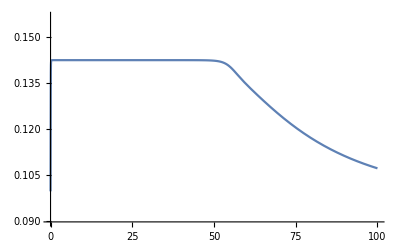

```mathematica
Plot[singleCellDKOGCaMP,{t,0,singleCellDKOMaxTime},PlotRange->{.9*minInt,1.1*maxInt}]
```

## Get 25 s contour (for testing purposes)

```mathematica
getHealTime[sol_]:=Check[FindRoot[sol==(minInt+maxInt)/2,{t,1,singleCellDKOMaxTime}],t->"fail"]
```

```mathematica
τScaleMin=.1;
τScaleMax=1.;
τScaleStep=.05;
rμTScaleMin=1.;
rμTScaleMax=2.5;
rμTScaleStep=.5;
```

```mathematica
contourPoints=Quiet@Flatten[Table[{#[[2]]*scaleτ,#[[1]]*scaleμ,t/.getHealTime[CtoF[singleCellDKOSolution@@ReplacePart[#,{2->#[[2]]*scaleτ,1->#[[1]]*scaleμ}]]]},{scaleτ,τScaleMin,τScaleMax,τScaleStep},{scaleμ,rμTScaleMin,rμTScaleMax,rμTScaleStep}]&@singleCellDKOEparams,1];
```

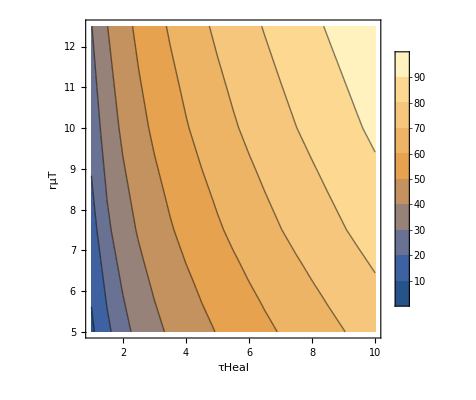

```mathematica
ListContourPlot[contourPoints,PlotLegends->Automatic,FrameLabel->{"τHeal","rμT"}]
```

```mathematica
healTimeInterpolation=Interpolation@contourPoints
```

InterpolatingFunction[…]

```mathematica
healTimeContour=Interpolation@(Table[Check[{#[[2]]*scaleτ,μ/.FindRoot[healTimeInterpolation[#[[2]]*scaleτ,μ]==25,{μ,#[[1]]*rμTScaleMin,#[[1]]*rμTScaleMax}]},Nothing],{scaleτ,τScaleMin,τScaleMax,τScaleStep}]&@singleCellDKOEparams)
```

InterpolatingFunction::dmval: Input value {2.,4.31674} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.,4.58962} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

InterpolatingFunction[…]

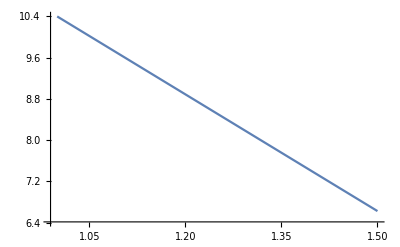

```mathematica
ListLinePlot@healTimeContour
```

## Functions to get final contour (real deal)

```mathematica
paramPosition[param_]:=First@First@Position[extParams,param];

getHealContour//ClearAll
getHealContour[
paramAssociation_?AssociationQ,
maxTime_?NumberQ,
{τHealMin_,τHealMax_,τHealStep_},
{rμTMin_,rμTMax_,rμTStep_}]:=
Block[
{params=paramAssociation/@extParams,
contoursPoints,
contoursPlot,
initRules,
singleCellDKOSolution,
interpolation,
healTimeContour},

(*initial stuff*)

initRules=getNewInits[paramAssociation];
singleCellDKOSolution=ParametricNDSolveValue[deqns/.intParams/.{jGJIP3->0.,jGJc->0.}/.initRules,c[t],{t,0,maxTime},extParams];
getHealTime[sol_]:=Check[FindRoot[sol==(minInt+maxInt)/2,{t,1,maxTime}],t->"fail"];

(*get heal time for each point in the 2D parameter space*)
contoursPoints=Quiet@Flatten[
Table[{τ,rμ,t/.getHealTime[CtoF[singleCellDKOSolution@@ReplacePart[params,{paramPosition[τHeal]->τ,paramPosition[rμT]->rμ}]]]},
{τ,τHealMin,τHealMax,τHealStep},
{rμ,rμTMin,rμTMax,rμTStep}
],1];

contoursPlot=ListContourPlot[contoursPoints,PlotLegends->Automatic,FrameLabel->{"μ-tear healing time (s)","maximum  flux  ratio"},FrameStyle->Directive[Black,16]];

(*get points from 25 second heal time*)
interpolation=Interpolation@contoursPoints;

healTimeContour=Quiet@Interpolation@(Table[Check[{τ,rμ/.FindRoot[interpolation[τ,rμ]==25,{rμ,rμTMin,rμTMax}]},Nothing],{τ,τHealMin,τHealMax,τHealStep}]);

Return[
{healTimeContour,
contoursPlot,
ListLinePlot[healTimeContour,PlotRange->All,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{"μ-tear healing time (s)","maximum  flux  ratio"},FrameStyle->Directive[Black,16],PlotStyle->{{Thick, Dashed,Black}}]
}
];

]
```

## Test

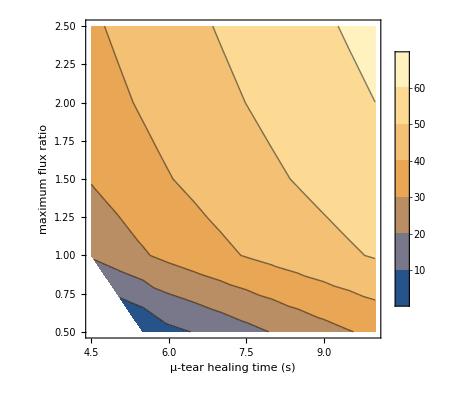
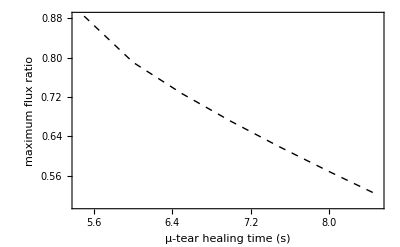
{InterpolatingFunction[…],-Graphics-,-Graphics-}

```mathematica
(*Test*)
getHealContour[singleCellDKOEparamsAssociation,100.,{4.5,10.,.5},{.5,2.5,.5}]
```

# Radial Cell Line

This section uses a 1D version of the model by assuming radial symmetry. This model is used to look at the first expansion in a control tissue. This part “works” closely with the previous section, since for a given parameter set we can pick out the 25 s heal time contour and determine parameter values for rμT and τHeal accordingly

## GJ Fluxes

```mathematica
volumeScale[ring_]:=If[ring≠1,8.*ring-8.,1.];
areaScale[ring_]:=If[ring≠1,8.*ring-8.,1.];

perimeterScale[ring_]:=2*ring-1
```

```mathematica
fluxGJCaTerms1D=
ηGJc*Join[
{(Subscript[c, 2][t]-Subscript[c, 1][t])},
Table[(If[i==ringsAblated,connectAblated,1.]*(perimeterScale[i]/volumeScale[i])*(Subscript[c, i+1][t]-Subscript[c, i][t])+If[i==ringsAblated+1,connectAblated,1.]*(perimeterScale[i-1]/volumeScale[i])*(Subscript[c, i-1][t]-Subscript[c, i][t])),{i,2,numRings-1}],
{(perimeterScale[numRings-1]/volumeScale[numRings])*(Subscript[c, numRings-1][t]-Subscript[c, numRings][t])}];

fluxGJIP3Terms1D=ηGJIP3*Join[
{(Subscript[ip3, 2][t]-Subscript[ip3, 1][t])},
Table[(If[i==ringsAblated,connectAblated,1.]*(perimeterScale[i]/volumeScale[i])*(Subscript[ip3, i+1][t]-Subscript[ip3, i][t])+If[i==ringsAblated+1,connectAblated,1.]*(perimeterScale[i-1]/volumeScale[i])*(Subscript[ip3, i-1][t]-Subscript[ip3, i][t])),{i,2,numRings-1}],
{(perimeterScale[numRings-1]/volumeScale[numRings])*(Subscript[ip3, numRings-1][t]-Subscript[ip3, numRings][t])}];
```

```mathematica
fluxGJCaTermsUW1D=
ηGJc*Join[
{(Subscript[c, 2][t]-Subscript[c, 1][t])},
Table[((perimeterScale[i]/volumeScale[i])*(Subscript[c, i+1][t]-Subscript[c, i][t])+(perimeterScale[i-1]/volumeScale[i])*(Subscript[c, i-1][t]-Subscript[c, i][t])),{i,2,numRings-1}],
{(perimeterScale[numRings-1]/volumeScale[numRings])*(Subscript[c, numRings-1][t]-Subscript[c, numRings][t])}];

fluxGJIP3TermsUW1D=ηGJIP3*Join[
{(Subscript[ip3, 2][t]-Subscript[ip3, 1][t])},
Table[((perimeterScale[i]/volumeScale[i])*(Subscript[ip3, i+1][t]-Subscript[ip3, i][t])+(perimeterScale[i-1]/volumeScale[i])*(Subscript[ip3, i-1][t]-Subscript[ip3, i][t])),{i,2,numRings-1}],
{(perimeterScale[numRings-1]/volumeScale[numRings])*(Subscript[ip3, numRings-1][t]-Subscript[ip3, numRings][t])}];
```

## Equations

```mathematica
(*Single-cell equations*)
modelEqns1D=deqns/.lr->0.;
```

```mathematica
(*Variable replacements for multiple cells*)
depVars1D=Table[Subscript[spec, i][t],{i,numRings},{spec,{ip3,h,c,cER}}];
variableReplacements1D=Flatten/@Table[{spec[t]->Subscript[spec, i][t],spec'[t]->Subscript[spec, i]'[t]},{i,numRings},{spec,{ip3,h,c,cER}}];
initReplacement1D=Flatten/@Table[{spec[0]->Subscript[spec, i][0]},{i,numRings},{spec,{ip3,h,c,cER}}]; 

(*Making ablated cells have constant calcium*)
ablatedChanges=Flatten@Table[If[i≤ringsAblated,{Subscript[c, i]'[t]==x_->Subscript[c, i]'[t]==0,Subscript[c, i][0]==x_->Subscript[c, i][0]==cExt},{Subscript[c, i]'[t]==x_->Subscript[c, i]'[t]==x,Subscript[c, i][0]==x_->Subscript[c, i][0]==x}],{i,numRings}];
```

### Putting it all together

```mathematica
(*Comapred to the equilibrium tissue, we add in the new resting levels from the previous section, and we take out the initial condition scaling (since we already have the initial conditions for each cell)*)
multiCellReplacements1D=
Table[

Join[
(*newEQs1D[[i]],*)
variableReplacements1D[[i]],
initReplacement1D[[i]],
{jGJIP3->fluxGJIP3Terms1D[[i]],jGJc->fluxGJCaTerms1D[[i]]},
{rμT->rμT*μTDist[ringPositions[[i]]]},
{r->If[i==1,dr*rd,Δx*(i-.5)]}
],

{i,numRings}];
```

```mathematica
tissueModelEquations1D=Flatten[modelEqns1D/.multiCellReplacements1D]/.ablatedChanges/.intParams;
```

```mathematica
tissueModelSol1D=
ParametricNDSolveValue[
tissueModelEquations1D,
depVars1D[[;;,3]],
{t,0,400.},
extParams,
DependentVariables->Flatten@depVars1D,
"Method"->{"EquationSimplification"->{Automatic,"TimeConstraint"->100}}];
```

```mathematica
association1D=
Association@{
rμT->1000.*.25/50.,
τHeal->10.,
rPMCA->.1,
kPMCA->.1,
rSOC->5.2565/50.,
ηNCX->50.,
nNCX->1.,
kNCX->8.,
rlkPM->1000*.002/50.,
α->0.,
α0->.1,
kl->.05,
nl->3.,
Kc->.4,
ηIPR->24.1,
ηSERCA->20.1,
kSERCA1->.1,
kSERCA2->0.,
ηlkER->.03,
Bx->5.,
ηGJIP3->.5,
ηGJc->10.,
connectAblated->0.
};

params1D=association1D/@extParams;
```

```mathematica
test=tissueModelSol1D@@params1D;
```

```mathematica
testG=CtoF/@test;
```

```mathematica
(*Function for getting Ca Rad vs time*)
getCaRad1D[sol_]:=
Table[{time,

Block[{grData=Transpose@{Table[If[rng==1,dr*rd,Δx*(rng-1)],{rng,numRings}],sol/.t->time},fCurrent=maxInt,rng=1,r1,r2,gLine},

While[fCurrent>(minInt+maxInt)/2&&rng<numRings,
rng+=1;
fCurrent=grData[[rng,2]];
r1=rng-1;
r2=rng;
];

(((grData[[r2,2]]-grData[[r1,2]])*(r1-.5)+(minInt+maxInt)/2-grData[[r1,2]])/(grData[[r2,2]]-grData[[r1,2]])-.5)*Δx

]},{time,Δt,41+Δt,Δt}]
```

```mathematica
getCaRad1D[testG]
```

{{2.14,51.1483},{4.28,54.8903},{6.42,56.2211},{8.56,56.9132},{10.7,56.441},{12.84,55.8429},{14.98,55.4115},{17.12,55.0219},{19.26,54.4318},{21.4,53.5596},{23.54,52.4201},{25.68,50.9916},{27.82,49.7248},{29.96,48.6564},{32.1,47.5296},{34.24,46.2194},{36.38,44.6667},{38.52,43.0312},{40.66,41.5944},{42.8,40.1286}}

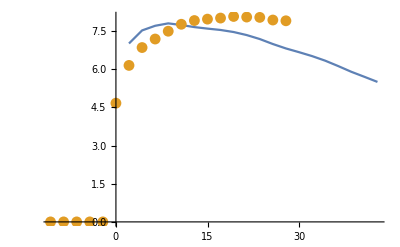

```mathematica
ListLinePlot[{getCaRad1D[testG]/.({t_,r_}->{t,r/Δx}),caRadData[[;;IntegerPart@(42/Δt)]]/.({t_,r_}->{t,r/Δx})},Joined->{True,False}]
```

```mathematica
caRadData[[;;IntegerPart@(42/Δt)]]
```

{{-10.7,0.},{-8.56,0.},{-6.42,0.},{-4.28,0.},{-2.14,0.},{0.,34.034},{2.14,44.8619},{4.28,49.9806},{6.42,52.425},{8.56,54.6642},{10.7,56.656},{12.84,57.7242},{14.98,58.1288},{17.12,58.4341},{19.26,58.8945},{21.4,58.7235},{23.54,58.6279},{25.68,57.8727},{27.82,57.6533}}

{RGBColor[0, 0, 1],RGBColor[Rational[1, 10], 0, Rational[9, 10]],RGBColor[Rational[1, 5], 0, Rational[4, 5]],RGBColor[Rational[3, 10], 0, Rational[7, 10]],RGBColor[Rational[2, 5], 0, Rational[3, 5]],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[Rational[3, 5], 0, Rational[2, 5]],RGBColor[Rational[7, 10], 0, Rational[3, 10]],RGBColor[Rational[4, 5], 0, Rational[1, 5]],RGBColor[Rational[9, 10], 0, Rational[1, 10]],RGBColor[1, 0, 0]}

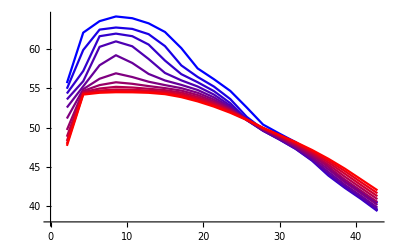

```mathematica
sweeps=Table[ReplacePart[association1D,Key@ηSERCA->association1D[ηSERCA]*scale],{scale,.5,1.5,.1}];
sweepParams=extParams/.sweeps;
sweepSols=tissueModelSol1D@@@sweepParams;
sweepSolsG=CtoF/@sweepSols;
sweepRads=getCaRad1D/@sweepSolsG;
colors=Table[RGBColor[r,0,1-r],{r,0,1,1/((Length@sweeps)-1)}]
ListLinePlot[sweepRads,PlotStyle->colors]
```

## Final Function

```mathematica
get1DSol//ClearAll
get1DSol[
paramAssociation_?AssociationQ,
maxTime_?NumberQ,
sweepParam_,
startRing_,
endRing_,
longTime_?BooleanQ]:=
Block[
{params=paramAssociation/@extParams,
eqns,
initRules,
solution1D,
solution1DLong,

sols,
cSols,
cERSols,
gcampSol1D,
caRad1D,

solsLong,

sweepSols,sweepRads,sweepPlot,colors,

longPlot
},


initRules=getNewInits@paramAssociation;
eqns=Flatten[(modelEqns1D/.initRules)/.multiCellReplacements1D]/.ablatedChanges/.intParams;
testing=eqns;
solution1D=
ParametricNDSolveValue[
eqns,
depVars1D[[;;,{3,4}]],
{t,0,maxTime},
extParams,
DependentVariables->Flatten@depVars1D,
"Method"->{"EquationSimplification"->{Automatic,"TimeConstraint"->100}}];

solution1DLong=
ParametricNDSolveValue[
eqns,
(CtoF/@depVars1D[[;;,3]])/.t->1000.,
{t,0,1000.},
extParams,
DependentVariables->Flatten@depVars1D,
"Method"->{"EquationSimplification"->{Automatic,"TimeConstraint"->100}}];

sols=solution1D@@params;
cSols=sols[[;;,1]];
cERSols=sols[[;;,2]];

gcampSol1D=CtoF/@cSols;
caRad1D=getCaRad1D[gcampSol1D];

(*If you want to sweep a parameter*)
If[!(sweepParam==="None"),
sweepSols=
If[sweepParam==="True ηNCX",
solution1D@@@(extParams/.Table[ReplacePart[paramAssociation,Append[(Key@#->paramAssociation[#]/scale)&/@{rμT,rPMCA,rSOC,rlkPM},Key@ηNCX->paramAssociation[ηNCX]*scale]],{scale,.5,1.5,.1}]),
solution1D@@@(extParams/.Table[ReplacePart[paramAssociation,Key@sweepParam->paramAssociation[sweepParam]*scale],{scale,.5,1.5,.1}])
];
sweepRads=getCaRad1D/@(CtoF/@(sweepSols[[;;,;;,1]]));
colors=Table[RGBColor[r,0,1-r],{r,0,1,1/((Length@sweepRads)-1)}];
sweepPlot=ListLinePlot[sweepRads,PlotStyle->colors,PlotRange->{Min[#[[;;,2]]]*.9,Max[#[[;;,2]]]*1.1},AxesLabel->{"t (s)","Ca^(2+) rad (μm)"},PlotLabel->ToString@sweepParam]&@caRadData[[;;IntegerPart@(42/Δt)]];,

sweepPlot="Plot was not generated";
];

(*If you want to look at long time solution*)
If[longTime,
solsLong=solution1DLong@@params;
longPlot=ListLinePlot[solsLong,
AxesLabel->{"distance from wound center (# cells)","resting GCaMP Fl."},
Epilog->{Gray,Line[{{5,minInt*.5},{5,maxInt*1.5}}]},
PlotRange->{minInt*.9,maxInt*1.1},
ImageSize->Large];,

longPlot="Plot at long time not generated"];

Return[
{
Plot[#,{t,0,maxTime},PlotRange->{.9*minInt,1.1*maxInt}]&/@gcampSol1D,
ListLinePlot[{caRad1D/.({t_,r_}->{t,r/Δx}),#/.({t_,r_}->{t,r/Δx})},Axes->False,Frame->{{True,False},{True,False}},Joined->{True,False},PlotLegends->{"Model","Data"},PlotRange->{{0,40},{Min[#[[;;,2]]]*.9,Max[#[[;;,2]]]*1.1}/Δx},FrameLabel->{"t (s)","Ca^(2+) Radius (# cells)"},FrameStyle->Directive[Black,16],PlotStyle->{Thick,Automatic}]&@caRadData[[;;IntegerPart@(42/Δt)]],
If[!(sweepParam==="None"),Show[sweepPlot,ListPlot[caRadData[[;;IntegerPart@(42/Δt)]],PlotStyle->{Black,PointSize@Medium}]],sweepPlot],
Plot[#,{t,0,maxTime},PlotRange->All]&/@cSols,
LogPlot[Evaluate@cSols[[startRing;;endRing]],{t,0,maxTime},PlotRange->All,PlotLegends->Range[startRing,endRing]],
longPlot,
gcampSol1D
}
];

]
```

# IP3 Spike Model

This second uses a “zoomed in” tissue to test for wave propagation capabilities in the model. The model has no damage, but it starts with an initial IP3 Spike in the center cell of the tissue. The goal is to obtain a propagative wave from this spike, and to (potentially) alter model parameters to obtain a wave that propagates at a speed and “width” similar to that in the data

## Tissue Model Setup

Using “zoomed in” tissue for testing IP3 spike model

### Mesh

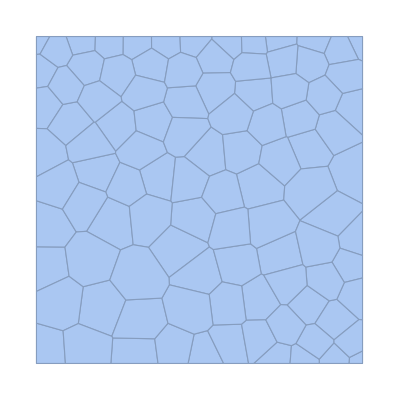

```mathematica
(*mesh=Import["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\Older Calcium Modeling and Misc\\mesh_4826cells_450x450.m"]
meshRatio=1.;*)
mesh=Import["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\Older Calcium Modeling and Misc\\mesh_100cells_450x450.m"]
meshRatio=.143;(*Just for testing purposes. This ratio takes the 100 cell mesh and changes the lengths to be comparable to the 4826 cell mesh*)
```

```mathematica
(*Get information about each cell*)
range=450.;(*From mesh file name (side length of grid in μm)*)

(*Get distances from center of mesh to each cell centroid*)
distances=Sqrt[(#[[1]]-range/2)^2+(#[[2]]-range/2)^2]&/@PropertyValue[{mesh,2},MeshCellCentroid]*meshRatio;
positions=PropertyValue[{mesh,2},MeshCellCentroid];

(*Get number of cells*)
numCells2D=Length@distances;
```

```mathematica
interiorCells=MeshCellIndex[mesh,{2,"Interior"}][[;;,2]];
```

```mathematica
areas=Area[#]&/@MeshPrimitives[mesh,2]*(10^-5)^2*meshRatio^2; (*Convert from μm^2 to dm^2*)
avgArea=Mean[areas[[interiorCells]]]
```

4.24043×10^-9

```mathematica
Δx=N[Sqrt[avgArea*(10^5)^2/π]]*2 (*Should be around 7.4*)
```

7.34784

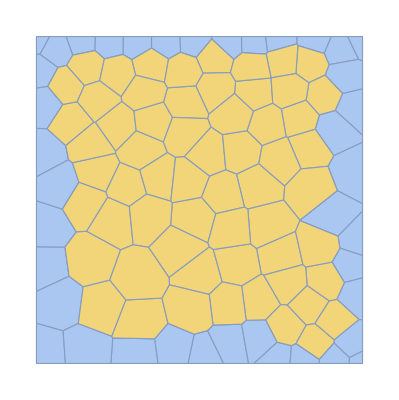

```mathematica
HighlightMesh[mesh,Thread[{2,MeshCellIndex[mesh,{2,"Interior"}][[;;,2]]}]]
```

### Make Adjacency Matrix

Create a nPts X nPts matrix that says whether or not a cell is adjacent to another cell. I cannot seem to find a built in function to do this, so I have to code it myself. Instead of making elements either 0 or 1, I make them 0 (not adjacent) or the length of the shared edge. This is because I will assume that the flux of ions/molecules through the gap junctions will be proportional to the length of the shared edge. The larger an edge is shared between cells, the more transfer we would expect due to more gap junctions being present.

```mathematica
(*Produce adjacency matrix with shared edge lengths as elements*)
Block[{conn,lengths,directions,positionVectors,sines,edges,adj},

(*Get connectivity matrix, which is a matrix whose rows represent a cell and column represents an edge associated with the cell*)
conn=mesh["ConnectivityMatrix"[2,1]]//Unitize//Normal;

(*Lengths of each edge*)
lengths=EuclideanDistance[#[[1]],#[[2]]]&@@@MeshPrimitives[mesh,1];

(*direction vectors of each edge*)
directions=#[[2]]-#[[1]]&@@@MeshPrimitives[mesh,1];

(*position vectors of the midpoints of each edge*)
positionVectors=((#[[1]]+#[[2]])/2-{range/2,range/2})&@@@MeshPrimitives[mesh,1];

(*List of Sin of angle between position vector of edge midpoint (relative to the wound center) and the direciton of the shared edge*)
sines=Table[Norm@Cross[Append[directions[[i]],0],Append[positionVectors[[i]],0]]/(Norm[directions[[i]]]*Norm[positionVectors[[i]]]),{i,Length@directions}];

(*List where each element is an edge and tells you which cell(s) have that edge*)
edges=(Position[#,1]&/@Transpose[conn])/.{e_}->e;

(*Initialize matrix*)
adj=ConstantArray[0.,{numCells2D,numCells2D}];

(*Function that replaces corresponding elements in the initial adjMat with an edge length if the cells in the row&column share that edge*)
alter[pos_,edge_]:=If[Length[pos]==2,adj[[pos[[1]],pos[[2]]]]=adj[[pos[[2]],pos[[1]]]]=lengths[[edge]]*If[gjPolarize,sines[[edge]],1.]];

MapIndexed[alter[#1,First[#2]]&,edges];

adjMat=SparseArray[adj]*meshRatio;
]
```

```mathematica
(*(*Check to make sure adjacencies are correct*)
Manipulate[HighlightMesh[HighlightMesh[mesh,Join[Thread[{2,Position[Normal[adjMat[[i]]],x_/;x≠0]//Flatten}]]],Style[{2,i},Red]],{i,1,numCells2D,1}]*)
```

### Random Values

```mathematica
(*GAP JUNCTIONS*)
gjRand=True; (*True = give each cell a random GJ parameter the tissue model. Value for a border determined by smallest value of the two cells that share that border*)
σGJ=.5;(*standard deviation for GJ randomness*)
gjPolarize=False; (*True = multiply GJ params by sinθ, where θ is the angle between the radial vector to a cell edge and the direction of the cell edge*)

(*GCaMP*)
gcampRand=True; (*True = randomize the amount of GCaMP in each cell. The random scale will also scale the fluorescence values of the model output*)
σgcamp=.1;(*standard deviation for gcamp randomizer*)
(*gcampRandVals=Abs@RandomVariate[NormalDistribution[1.,σgcamp],numCells2D];*)
gcampRandVals=RandomVariate[LogNormalDistribution[-(.1)^2/2,.1],numCells2D];

maxGCAMPVal=Max@gcampRandVals; (*Needed to determine how to scale video output later*)

(*PLC*)
plcRand=False; (*True = randomize PLC (parameter α) between cells*)
σPLC=.5; (*standard deviation for PLC randomizer*)
(*plcRandVals=Abs@RandomVariate[NormalDistribution[1.,σPLC],numCells2D];*)
plcRandVals=RandomVariate[LogNormalDistribution[-(.4)^2/2,.4],numCells2D];
```

### GJ Fluxes

```mathematica
(*random GJ values. Make sure none of them are negative*)
(*randGJmults=If[gjRand,Abs@RandomVariate[NormalDistribution[1.,σGJ],numCells2D],ConstantArray[1.,numCells2D]];*)
randGJmults=If[gjRand,RandomVariate[LogNormalDistribution[-(.4)^2/2,.4],numCells2D],ConstantArray[1.,numCells2D]];
```

```mathematica
(*η values are based on a single "ideal" cell of diameter Δx, with flux through its entire perimeter. Therefore, in order to properly scale based on cell volume and shared perimeter between two cells, the GJ fluxes have to be scaled by (v0/Subscript[v, i])*(aij/a0), where the 0 subscript denotes the "ideal" cell, i is the cell in question, and j denotes any cell adjacent to i. Since all cells have the same height, volume ratios are reduced to ratios of PM area, and shared areas are reduced to lengths. So v0 becomes the PM area of the ideal cell, and a0 becomes the circumference of the ideal cell.

a0 and areas are in dm^2, adjMat lengths and Δx are in μm. So the ratios work out to be dimensionless*)
fluxGJCaTerms2D=Table[ηGJc*Total[(Min[randGJmults[[i]],randGJmults[[#]]]*(a0/areas[[i]])*(adjMat[[i,#]]/(π*Δx))*(Subscript[c, #][t]-Subscript[c, i][t]))&/@(Flatten@adjMat[[i]]["NonzeroPositions"])],{i,numCells2D}];
fluxIP3Terms2D=Table[ηGJIP3*Total[(Min[randGJmults[[i]],randGJmults[[#]]]*(a0/areas[[i]])*(adjMat[[i,#]]/(π*Δx))(Subscript[ip3, #][t]-Subscript[ip3, i][t]))&/@(Flatten@adjMat[[i]]["NonzeroPositions"])],{i,numCells2D}];

(*Unwounded terms; only difference is the part with ablation connection*)
fluxGJCaTerms2DUW=Table[ηGJc*Total[(Min[randGJmults[[i]],randGJmults[[#]]]*(a0/areas[[i]])*(adjMat[[i,#]]/(π*Δx))*(Subscript[c, #][t]-Subscript[c, i][t]))&/@(Flatten@adjMat[[i]]["NonzeroPositions"])],{i,numCells2D}];
fluxIP3Terms2DUW=Table[ηGJIP3*Total[(Min[randGJmults[[i]],randGJmults[[#]]]*(a0/areas[[i]])*(adjMat[[i,#]]/(π*Δx))(Subscript[ip3, #][t]-Subscript[ip3, i][t]))&/@(Flatten@adjMat[[i]]["NonzeroPositions"])],{i,numCells2D}];
```

## IP3 Spike

```mathematica
(*Find cell closest to the center*)
spikeCell=First@Ordering@distances;
```

```mathematica
(*Single-Cell equations*)
modelEqns2D=deqns/.{lr->0.};
```

### Scaling variables

```mathematica
(*Variable replacements for multiple cells*)
depVars2D=Table[Subscript[spec, i][t],{i,numCells2D},{spec,{ip3,h,c,cER}}];
variableReplacements2D=Flatten/@Table[{spec[t]->Subscript[spec, i][t],spec'[t]->Subscript[spec, i]'[t]},{i,numCells2D},{spec,{ip3,h,c,cER}}];
initReplacement2D=Flatten/@Table[If[i==spikeCell&&spec===ip3,{spec[0]->Subscript[spec, i][0]/ip3SpikeScale},{spec[0]->Subscript[spec, i][0]}],{i,numCells2D},{spec,{ip3,h,c,cER}}];
```

### Putting it all together

```mathematica
(*Comapred to the equilibrium tissue, we add in the new resting levels from the previous section, and we take out the initial condition scaling (since we already have the initial conditions for each cell)*)
multiCellReplacements2D=
Table[

Join[
variableReplacements2D[[i]],
initReplacement2D[[i]],
{Bx->Bx*If[gcampRand,gcampRandVals[[i]],1.]},
{α->α*If[plcRand,plcRandVals[[i]],1.]},
(*{α0->α0*If[plcRand,plcRandVals[[i]],1.]},*)
{jGJIP3->fluxIP3Terms2DUW[[i]],jGJc->fluxGJCaTerms2DUW[[i]]},
{r->distances[[i]]}
],

{i,numCells2D}];
```

```mathematica
tissueCellEquations=modelEqns2D/.multiCellReplacements2D;

tissueModelEquations=Flatten[Table[tissueCellEquations[[i]],{i,numCells2D}]]/.intParams;
```

```mathematica
tissueModelSol=
ParametricNDSolveValue[
tissueModelEquations,
depVars2D[[;;,3]],
{t,0,400.},
Append[extParams,ip3SpikeScale],
DependentVariables->Flatten@depVars2D,
"Method"->{"EquationSimplification"->{Automatic,"TimeConstraint"->100}}];
```

```mathematica
association2D=
Association@{
rμT->0.*1000.*.25/50.,
τHeal->10.,
rPMCA->.1,
kPMCA->.1,
rSOC->5.2565/50.,
ηNCX->50.,
nNCX->1.,
kNCX->8.,
rlkPM->1000*.002/50.,
α->3.,
α0->.1,
kl->.05,
nl->3.,
Kc->.4,
ηIPR->24.1,
ηSERCA->20.1,
kSERCA1->.1,
kSERCA2->0.,
ηlkER->.03,
Bx->5.,
ηGJIP3->.5,
ηGJc->10.,
ip3SpikeScale->10000.,
connectAblated->0.
};

params2D=association2D/@Append[extParams,ip3SpikeScale];
```

```mathematica
test=tissueModelSol@@params2D;
```

```mathematica
testG=CtoF/@test;
```

### Animation

```mathematica
(*Set frames before wounding to be resting calcium levels*)
```

```mathematica
animate2D[soln_,maxTime_]:=
Block[{timePoints,minF,maxF,styles,animList,frames},
timePoints=Table[soln[[i]]/.t->τ,{τ,0.,maxTime,Δt},{i,numCells2D}];

minF=.12;
maxF=1.;

styles=
Table[Style[{2,i},GrayLevel[Min[maxF,If[gcampRand,gcampRandVals[[i]],1.]*Rescale[timePoints[[τ,i]],{minInt,maxInt*maxGCAMPVal},{minF,maxF}]]]],{τ,Length@timePoints},{i,numCells2D}];

animList=HighlightMesh[mesh,#,MeshCellStyle->{1->Directive[Opacity[0],Antialiasing->False]}]&/@styles;

frames=MapIndexed[Show[#1,Graphics[{White,Text[Style["t = "<>ToString[Round[Δt*(First[#2]-1),.1]]<>" s",White,18],{75,35}],Text[Style["10 μm",White,18],{range*.825,range*.15}],Thickness@.025,Line[{{range*.75,range*.1},{range*.75+(10/meshRatio),range*.1}}]}]]&,animList];

Return[frames]

(*ListAnimate[frames,7]*)
]
```

```mathematica
frames2D=animate2D[testG];
```

```mathematica
(*(*ListAnimate[frames2D,7]*)
SetDirectory[NotebookDirectory[]];
Export["spikeTest.avi",frames2D,"FrameRate"->10];*)
```

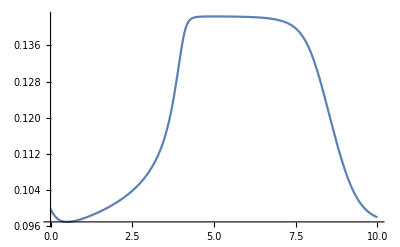

```mathematica
Plot[testG[[spikeCell+1]],{t,0,10},PlotRange->All]
```

## Final Function

```mathematica
getIP3SpikeSol//ClearAll
getIP3SpikeSol[
paramAssociation_?AssociationQ,
maxTime_?NumberQ,
ip3SpikeScaleP_?NumberQ]:=
Block[
{params=Append[paramAssociation/@extParams,ip3SpikeScaleP],
initRules,
eqnsCell,
eqnsModel,
solution2D,

gcampSol2D,
frames
},

initRules=getNewInits[paramAssociation];
eqnsCell=(modelEqns2D/.initRules)/.multiCellReplacements2D;

eqnsModel=Flatten[Table[eqnsCell[[i]],{i,numCells2D}]]/.intParams;

solution2D=
ParametricNDSolveValue[
eqnsModel,
depVars2D[[;;,3]],
{t,0,maxTime},
Append[extParams,ip3SpikeScale],
DependentVariables->Flatten@depVars2D,
"Method"->{"EquationSimplification"->{Automatic,"TimeConstraint"->100}}];

gcampSol2D=CtoF/@(solution2D@@params);
frames=animate2D[gcampSol2D,maxTime];

Return[
{
frames
}
];

]
```

# Full Single-Cell Model

This section looks at the full single-cell model. While μT damage can be included, the main point of this is to investigate single-cell responses to the damage signal of the second expansion. Checking that the calcium signal does not go too far away from the wound, to check on calcium oscillations, time delay of the second expansion, etc. This should be the final step of parameter tweaking before moving onto full-tissue runs on ACCRE.

```mathematica
modelEqnsSingleCell=deqns/.intParams/.{lr->lrSol[r,t],jGJIP3->0.,jGJc->0.};
```

```mathematica
fluxes=β*{jIPR,-jSERCA,jlkER,ηNCX*jSOC,-ηNCX*jPMCA,-ηNCX*jNCX,ηNCX*jlkPM,ηNCX*jμT}/.intParams;
```

```mathematica
modelSolSingleCell=ParametricNDSolveValue[modelEqnsSingleCell,{ip3[t],c[t],cER[t],h[t],CtoF[c[t]],Append[fluxes,Total@fluxes]},{t,0,tEnd},Prepend[extParams,r],DependentVariables->{ip3[t],c[t],cER[t],h[t]}];
```

```mathematica
getSingleCellSol//ClearAll
getSingleCellSol[
paramAssociation_?AssociationQ,
maxTime_?NumberQ,
dist_?NumberQ,
sweepParam_]:=
Block[
{params=Prepend[paramAssociation/@extParams,#]&/@{1.,75.,120.,170.,dist},

initRules,
solution,
sweepPlot,
sweepSols,

singleCellOutput,

legend={"r= 0 μm (Wound Center)","r = 75 μm (Max 1^st Exp.)","r = 120 μm (Max 2^nd Exp.)","r = 170 μm (No Response)","r = "<>ToString[dist]<>" μm"}
},

initRules=getNewInits[paramAssociation];
solution=
ParametricNDSolveValue[modelEqnsSingleCell/.initRules,{ip3[t],c[t],cER[t],h[t],CtoF[c[t]],Append[fluxes,Total@fluxes]},{t,0,maxTime},Prepend[extParams,r],DependentVariables->{ip3[t],c[t],cER[t],h[t]}];

singleCellOutput=solution@@@params;

(*If you want to sweep a parameter*)
If[!(sweepParam==="None"),
sweepSols=
If[sweepParam==="True ηNCX",
solution@@@(Prepend[extParams,dist]/.Table[ReplacePart[paramAssociation,Append[(Key@#->paramAssociation[#]/scale)&/@{rμT,rPMCA,rSOC,rlkPM},Key@ηNCX->paramAssociation[ηNCX]*scale]],{scale,.5,1.5,.25}]),
solution@@@(Prepend[extParams,dist]/.Table[ReplacePart[paramAssociation,Key@sweepParam->paramAssociation[sweepParam]*scale],{scale,.5,1.5,.25}])
];
colors=Table[RGBColor[r,0,1-r],{r,0,1,1/((Length@sweepSols)-1)}];
sweepPlot=Plot[Evaluate@sweepSols[[;;,5]],{t,0,maxTime},PlotStyle->colors,PlotRange->{minInt*.9,maxInt*1.1},AxesLabel->{"t (s)","Ca^(2+) rad (μm)"},PlotLabel->ToString@sweepParam],

sweepPlot="Plot was not generated";
];

Return[
{
Plot[Evaluate@singleCellOutput[[;;,5]],{t,0,maxTime},
PlotRange->{.9*minInt,1.1*maxInt},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{"time (s)","GCaMP Fluorescence Intensity"},
FrameStyle->Directive[Black,18],
PlotLegends->legend,
Epilog->
{Gray,
Line[{{35,.9*minInt},{35,1.1*maxInt}}],
Line[{{94,.9*minInt},{94,1.1*maxInt}}],
Line[{{0,Mean[{minInt,maxInt}]},{1000,Mean[{minInt,maxInt}]}}],

Black,
Text["None",{20,1.05*maxInt}],
Text["Second Exp.",{65,1.05*maxInt}],
Text["Flares",{220,1.05*maxInt}]
}],
Plot[Evaluate@singleCellOutput[[;;,2]],{t,0,maxTime},PlotRange->All,AxesLabel->{"t (s)","[Ca^(2+)] (μM)"},PlotLegends->legend],
Plot[Evaluate@singleCellOutput[[;;,3]],{t,0,maxTime},PlotRange->All,AxesLabel->{"t (s)","[Ca^(2+)]_ER (μM)"},PlotLegends->legend],
Plot[Evaluate@singleCellOutput[[;;,1]],{t,0,maxTime},PlotRange->All,AxesLabel->{"t (s)","[IP_3] (μM)"},PlotLegends->legend],
Plot[Evaluate@singleCellOutput[[;;,4]],{t,0,maxTime},PlotRange->All,AxesLabel->{"t (s)","h"},PlotLegends->legend],
Plot[Evaluate@singleCellOutput[[-1,6]],{t,0,maxTime},PlotRange->All,AxesLabel->{"t (s)","GCaMP Fl"},
PlotLegends->{"jIPR","jSERCA","jlkER","jSOC","jPMCA","jNCX","jlkPM","jμT","jTotal"}],
sweepPlot
}
];

]
```

# Putting it all together

A Manipulate function to do all parameter tweaking in one place.

```mathematica
(*Initializations*)

(*parameter set to load as starting settings*)
paramLoad=<|rμT->41.14497773461118,τHeal->5.25,rPMCA->0.12,kPMCA->0.1,rSOC->0.15000000000000002,ηNCX->10.,nNCX->2.5,kNCX->1.6,rlkPM->0.00025,α->0.9,α0->0.1,kl->0.05,nl->5.,Kc->0.4,ηIPR->4.,ηSERCA->5.,kSERCA1->0.1,kSERCA2->0.,ηlkER->0.01,Bx->5.,ηGJIP3->4.,ηGJc->2.,connectAblated->0.025|>;

contourInfo="Contour has not been generated";
updateContour=False;

info1D="1D Model has not been updated";
update1D=False;

info2D="2D Model has not been updated";
update2D=False;

infoSS="Single Cell Model has not been updated";
updateSS=False;

Manipulate[
Block[
{paramAssociation
},

(*rμT value is irrelevant before contour is set*)
paramAssociation=
Association@{rμT->If[!(contourInfo==="Contour has not been generated"),contourInfo[[1]][τHealP]/μTConversion,5.],τHeal->τHealP,rPMCA->rPMCAP,kPMCA->kPMCAP,rSOC->rSOCP,ηNCX->ηNCXP,nNCX->nNCXP,kNCX->kNCXP,rlkPM->rlkPMP,α->αP,α0->α0P,kl->klP,nl->nlP,Kc->KcP,ηIPR->ηIPRP,ηSERCA->ηSERCAP,kSERCA1->kSERCA1P,kSERCA2->kSERCA2P,ηlkER->ηlkERP,Bx->BxP,ηGJIP3->ηGJIP3P,ηGJc->ηGJcP,connectAblated->connectAblatedP};

finalParamAssociation=paramAssociation;

(*Update heal contour for τHeal and rμT. Update rμT*)
If[updateContour,
(*if update contour*)
contourInfo=getHealContour[ReplacePart[paramAssociation,Key@α->0.],maxTimeRangeDKO,{τMin,τMax,τStep},{rμTMin,rμTMax,rμTStep}]; 
updateContour=False;
paramAssociation=
Association@{rμT->contourInfo[[1]][τHealP]/μTConversion,τHeal->τHealP,τHealHDRatio->τHealHDRatioP,rPMCA->rPMCAP,kPMCA->kPMCAP,rSOC->rSOCP,ηNCX->ηNCXP,nNCX->nNCXP,kNCX->kNCXP,rlkPM->rlkPMP,α->αP,α0->α0P,kl->klP,nl->nlP,Kc->KcP,ηIPR->ηIPRP,ηSERCA->ηSERCAP,kSERCA1->kSERCA1P,kSERCA2->kSERCA2P,ηlkER->ηlkERP,Bx->BxP,ηGJIP3->ηgGJP3P,ηGJc->ηGJcP,connectAblated->connectAblatedP};,

(*If not update contour*)
"Contour has not been generated"
];

(*Update 1D model*)
If[update1D,
(*info1D=get1DSol[ReplacePart[paramAssociation,Key@α->0.],maxTimeRange1D];*)
info1D=get1DSol[paramAssociation,maxTimeRange1D,sweepParamRad,startRing,endRing,longTime];
update1D=False;,

"1D Model is not Updated"];

(*Update 2D model*)
If[update2D,
info2D=getIP3SpikeSol[ReplacePart[paramAssociation,{Key@α->plcScale*paramAssociation[α],Key@rμT->0.}],maxTimeRange2D,ip3SpikeScale];
update2D=False;,

"2D Model is not Updated"];

(*Update Single Cell model*)
If[updateSS,
infoSS=getSingleCellSol[ReplacePart[paramAssociation,{Key@rμT->0.}],maxTimeRangeSS,distance,sweepParamSS];
updateSS=False;,

"Single Cell Model is not Updated"];



(*Main Display Switch*)
Switch[mainView,

(*Display of the heal contour*)
"Heal Contour",
If[!(contourInfo==="Contour has not been generated"),
Switch[contourView,
"25 s",
Show[contourInfo[[3]](*,Graphics[{Red,PointSize@Large,Point[{τHealP,contourInfo[[1]][τHealP]}]}]*)],

"All",
contourInfo[[2]],

"Both",
Show[contourInfo[[2]],contourInfo[[3]]]],

contourInfo],

(*Display of 1D model*)
"1D model",
If[!(info1D==="1D Model hsa not been updated"),
Switch[view1D,
"Ca^(2+) Rad",
info1D[[2]],

"GCaMP",
Manipulate[
info1D[[1,ring]],
{ring,1,Length@info1D[[1]],1}],

"Ca^(2+)",
Manipulate[
info1D[[4,ring]]
,{ring,1,Length@info1D[[4]],1}],

"Ca^(2+) All",
info1D[[5]],

"Sweep",
info1D[[3]],

"Long Time",
info1D[[6]]
],

info1D

],

(*Display of IP3 Spike*)
"IP3 Spike",
If[!(info2D==="2D Model has not been updated"),
Manipulate[info2D[[1,i]],{i,1,Length@info2D[[1]],1}]
,
info2D
],

(*Display of the full single cell model*)
"Single-Cell",
If[!(infoSS==="Single Cell Model hsa not been updated"),
Switch[viewSS,
"GCaMP",infoSS[[1]],
"Ca^(2+)",infoSS[[2]],
"Ca_ER^(2+)",infoSS[[3]],
"IP_3",infoSS[[4]],
"h",infoSS[[5]],
"fluxes",infoSS[[6]],
"sweep",infoSS[[7]]
]
,
infoSS
]
]

]
,

Row[{

Column@{
Control@{mainView,{"Heal Contour","1D model","IP3 Spike","Single-Cell"}},
Style["Model Parameters",16,Bold],
Control@{τHealP,paramLoad[[Key@τHeal]]},
Control@{rPMCAP,paramLoad[[Key@rPMCA]]},
Control@{kPMCAP,paramLoad[[Key@kPMCA]]},
Control@{rSOCP,paramLoad[[Key@rSOC]]},
Control@{ηNCXP,paramLoad[[Key@ηNCX]]},
Control@{nNCXP,paramLoad[[Key@nNCX]]},
Control@{kNCXP,paramLoad[[Key@kNCX]]},
Control@{rlkPMP,paramLoad[[Key@rlkPM]]},
Control@{αP,paramLoad[[Key@α]]},
Control@{α0P,paramLoad[[Key@α0]]},
Control@{klP,paramLoad[[Key@kl]]},
Control@{nlP,paramLoad[[Key@nl]]},
Control@{KcP,paramLoad[[Key@Kc]]},
Control@{ηIPRP,paramLoad[[Key@ηIPR]]},
Control@{ηSERCAP,paramLoad[[Key@ηSERCA]]},
Control@{kSERCA1P,paramLoad[[Key@kSERCA1]]},
Control@{kSERCA2P,paramLoad[[Key@kSERCA2]]},
Control@{ηlkERP,paramLoad[[Key@ηlkER]]},
Control@{BxP,paramLoad[[Key@Bx]]},
Control@{ηGJIP3P,paramLoad[[Key@ηGJIP3]]},
Control@{ηGJcP,paramLoad[[Key@ηGJc]]},
Control@{connectAblatedP,paramLoad[[Key@connectAblated]]}
},

Column@{
Style["Heal Contour Settings",16,Bold],
Button["Update Contour",updateContour=True;],
Control@{maxTimeRangeDKO,100.},
Control@{τMin,1.},
Control@{τMax,6.},
Control@{τStep,.5},
Control@{rμTMin,1.},
Control@{rμTMax,10.},
Control@{rμTStep,1.},
Control@{contourView,{"All","25 s","Both"}},

Style["Radial Cell Line Settings",16,Bold],
Button["Update 1D Model",update1D=True;],
Control@{maxTimeRange1D,100.},
Control@{view1D,{"Ca^(2+) Rad","GCaMP","Ca^(2+)","Ca^(2+) All","Sweep","Long Time"}},
Control@{sweepParamRad,Append[Prepend[extParams,"None"],"True ηNCX"]},
Control@{{startRing,7},Range[1,numRings]},
Control@{{endRing,11},Reverse@Range[1,numRings]},
Control@{{longTime,False},{True,False}}},

Column@{
Style["IP3 Spike Settings",16,Bold],
Button["Update Ip3 Spike Model",update2D=True;],
Control@{maxTimeRange2D,20.},
Control@{plcScale,3.5},
Control@{ip3SpikeScale,1000.},

Style["Single Cell Settings",16,Bold],
Button["Update Single Cell Model",updateSS=True;],
Control@{maxTimeRangeSS,400.},
Control@{distance,200.},
Control@{viewSS,{"GCaMP","Ca^(2+)","Ca_ER^(2+)","IP_3","h","fluxes","sweep"}},
Control@{sweepParamSS,Append[Prepend[extParams,"None"],"True ηNCX"]}
}
}],

SynchronousUpdating->False]
```

### “saved”

First good one

```mathematica
(*Control@{τHealP,3.75},
Control@{rPMCAP,.08},
Control@{kPMCAP,.1},
Control@{rSOCP,.265},
Control@{ηNCXP,15.},
Control@{nNCXP,1.},
Control@{kNCXP,10.},
Control@{rlkPMP,.0005},
Control@{αP,.5562},
Control@{α0P,.1},
Control@{klP,.05},
Control@{nlP,5.},
Control@{KcP,.4},
Control@{ηIPRP,8.4},
Control@{ηSERCAP,10.1},
Control@{kSERCA1P,.1},
Control@{kSERCA2P,0.},
Control@{ηlkERP,.02},
Control@{BxP,5.},
Control@{ηGJIP3P,4.},
Control@{ηGJcP,4.}*)
```

Different single-cell response, but good first expansion. Lowered ER fluxes. Lower first expansion sensitivity to ER fluxes?

```mathematica
(*finalParamAssociation*)
```

```mathematica
(*Control@{τHealP,6.},
Control@{rPMCAP,.08},
Control@{kPMCAP,.1},
Control@{rSOCP,.1},
Control@{ηNCXP,15.},
Control@{nNCXP,1.},
Control@{kNCXP,10.},
Control@{rlkPMP,.00025},
Control@{αP,1.},
Control@{α0P,.05},
Control@{klP,.05},
Control@{nlP,5.},
Control@{KcP,.4},
Control@{ηIPRP,4.},
Control@{ηSERCAP,5.},
Control@{kSERCA1P,.1},
Control@{kSERCA2P,0.},
Control@{ηlkERP,.01},
Control@{BxP,5.},
Control@{ηGJIP3P,4.},
Control@{ηGJcP,4.}*)
```

```mathematica
(*11-22-21*)
<|rμT->39.786776046703196,τHeal->3.,rPMCA->0.08,kPMCA->0.1,rSOC->0.11,ηNCX->10.,kNCX->10.,rlkPM->0.00025,α->1.71,α0->0.1,kl->0.05,nl->5.,Kc->0.4,ηIPR->1.,ηSERCA->5.,kSERCA1->0.1,kSERCA2->0.,ηlkER->0.01,Bx->5.,ηGJIP3->4.,ηGJc->4.|>
```

<|rμT→39.7868,τHeal→3.,rPMCA→0.08,kPMCA→0.1,rSOC→0.11,ηNCX→10.,kNCX→10.,rlkPM→0.00025,α→1.71,α0→0.1,kl→0.05,nl→5.,Kc→0.4,ηIPR→1.,ηSERCA→5.,kSERCA1→0.1,kSERCA2→0.,ηlkER→0.01,Bx→5.,ηGJIP3→4.,ηGJc→4.|>

```mathematica
(*12-1-21*)
<|rμT->49.56135368822545,τHeal->4.25,rPMCA->0.08,kPMCA->0.1,rSOC->0.1,ηNCX->10.,nNCX->2.5,kNCX->1.6,rlkPM->0.00025,α->1.,α0->0.1,kl->0.05,nl->5.,Kc->0.4,ηIPR->4.,ηSERCA->5.,kSERCA1->0.1,kSERCA2->0.,ηlkER->0.01,Bx->5.,ηGJIP3->4.,ηGJc->2.|>
```

<|rμT→49.5614,τHeal→4.25,rPMCA→0.08,kPMCA→0.1,rSOC→0.1,ηNCX→10.,nNCX→2.5,kNCX→1.6,rlkPM→0.00025,α→1.,α0→0.1,kl→0.05,nl→5.,Kc→0.4,ηIPR→4.,ηSERCA→5.,kSERCA1→0.1,kSERCA2→0.,ηlkER→0.01,Bx→5.,ηGJIP3→4.,ηGJc→2.|>

```mathematica
(*12-9-21; same as above but with connectAblated as a non-zero parameter*)
<|rμT->49.56135368822545,τHeal->4.25,rPMCA->0.08,kPMCA->0.1,rSOC->0.1,ηNCX->10.,nNCX->2.5,kNCX->1.6,rlkPM->0.00025,α->1.,α0->0.1,kl->0.05,nl->5.,Kc->0.4,ηIPR->4.,ηSERCA->5.,kSERCA1->0.1,kSERCA2->0.,ηlkER->0.01,Bx->5.,ηGJIP3->4.,ηGJc->2.,connectAblated->0.0015|>
```

<|rμT→49.5614,τHeal→4.25,rPMCA→0.08,kPMCA→0.1,rSOC→0.1,ηNCX→10.,nNCX→2.5,kNCX→1.6,rlkPM→0.00025,α→1.,α0→0.1,kl→0.05,nl→5.,Kc→0.4,ηIPR→4.,ηSERCA→5.,kSERCA1→0.1,kSERCA2→0.,ηlkER→0.01,Bx→5.,ηGJIP3→4.,ηGJc→2.,connectAblated→0.0015|>

```mathematica
(*12-12-21 a tweak on the above to 
1) Increase rPMCA and rSOC to give them more of a noticable effect in the knockdown,
    2) Increase connectedAblated parameter since it was too weak,
      3) Slightly lower α since the flares were going a little too far for my liking*)

<|rμT->41.14497773461118,τHeal->5.25,rPMCA->0.12,kPMCA->0.1,rSOC->0.15000000000000002,ηNCX->10.,nNCX->2.5,kNCX->1.6,rlkPM->0.00025,α->0.9,α0->0.1,kl->0.05,nl->5.,Kc->0.4,ηIPR->4.,ηSERCA->5.,kSERCA1->0.1,kSERCA2->0.,ηlkER->0.01,Bx->5.,ηGJIP3->4.,ηGJc->2.,connectAblated->0.025|>
```

<|rμT→41.145,τHeal→5.25,rPMCA→0.12,kPMCA→0.1,rSOC→0.15,ηNCX→10.,nNCX→2.5,kNCX→1.6,rlkPM→0.00025,α→0.9,α0→0.1,kl→0.05,nl→5.,Kc→0.4,ηIPR→4.,ηSERCA→5.,kSERCA1→0.1,kSERCA2→0.,ηlkER→0.01,Bx→5.,ηGJIP3→4.,ηGJc→2.,connectAblated→0.025|>

```mathematica
(*1-4-22
Trying a first expansion that goes a little farther but decays quicker as well. Other parameters are adjusted accordingly*)
<|rμT->101.28200925591425,τHeal->3.,rPMCA->0.12,kPMCA->0.1,rSOC->0.15,ηNCX->13.,nNCX->2.5,kNCX->1.6,rlkPM->0.00025,α->0.9,α0->0.075,kl->0.05,nl->5.,Kc->0.4,ηIPR->4.,ηSERCA->5.,kSERCA1->0.1,kSERCA2->0.,ηlkER->0.01,Bx->5.,ηGJIP3->4.,ηGJc->2.,connectAblated->0.025|>
```

<|rμT→101.282,τHeal→3.,rPMCA→0.12,kPMCA→0.1,rSOC→0.15,ηNCX→13.,nNCX→2.5,kNCX→1.6,rlkPM→0.00025,α→0.9,α0→0.075,kl→0.05,nl→5.,Kc→0.4,ηIPR→4.,ηSERCA→5.,kSERCA1→0.1,kSERCA2→0.,ηlkER→0.01,Bx→5.,ηGJIP3→4.,ηGJc→2.,connectAblated→0.025|>

# Final Model

Final code for testing a parameter set chosen above. This code is tested using the “zoomed in mesh”, but the goal is to move this to ACCRE to run on the full mesh. Ideally only the Initialization section as well as this section are the only things that will need to go to ACCRE; the other sections should be removed when making the ACCRE notebook, as they are just for the purpose of testing the parameters.

```mathematica
finalParamAssociation=<|rμT->41.14497773461118,τHeal->5.25,rPMCA->0.12,kPMCA->0.1,rSOC->0.15000000000000002,ηNCX->10.,nNCX->2.5,kNCX->1.6,rlkPM->0.00025,α->0.9,α0->0.1,kl->0.05,nl->5.,Kc->0.4,ηIPR->4.,ηSERCA->5.,kSERCA1->0.1,kSERCA2->0.,ηlkER->0.01,Bx->5.,ηGJIP3->8.,ηGJc->4.,connectAblated->0.025|>;
```

## Initializations

```mathematica
(*List of strings to specify model components to knockout by 70% in one half of the tissue. Current options are GJ, PLC, SERCA, SOC, PMCA. Note that GJs are handled separately when GJ terms are made, since the GJ parameters are specific to cell-cell boundaries rather than single cells.*)
knockoutVal=.3(*percentage to keep for knockout (so 1 - this for percent knockdown)*);
knockoutList={};

(*knockout commands that do not require user input*)
knockoutAssociations=
<|"GJ"->Nothing,
"PLC"->({α->#*α(*,α0->#*α0*)}),
"SERCA"->(ηSERCA->#*ηSERCA),
"SOC"->(ηSOC->#*ηSOC),
"PMCA"->(ηPMCA->#*ηPMCA)|>&@knockoutVal;

knockoutRules=Flatten[knockoutAssociations/@knockoutList];


(*List of strings to specify model components to overexpress by 100% in one half of the tissue. Current options are PLC.*)
overExpressVal=2.(*overexpression factor*);
overExpressList={};

(*knockout commands that do not require user input*)
overExpressAssociations=<|"PLC"->({α->#*α(*,α0->#*α0*)})|>&@overExpressVal;

overExpressRules=Flatten[overExpressAssociations/@overExpressList];
```

```mathematica
gjRand=True; (*True = give each cell a random GJ parameter the tissue model. Value for a border determined by smallest value of the two cells that share that border*)
σGJ=.4;(*σ parameter for GJ randomness*)
gjPolarize=False; (*True = multiply GJ params by sinθ, where θ is the angle between the radial vector to a cell edge and the direction of the cell edge*)

gcampRand=True; (*True = randomize the amount of GCaMP in each cell. The random scale will also scale the fluorescence values of the model output*)
σgcamp=.1;(*σ parameter for gcamp randomizer*)

plcRand=False; (*True = randomize PLC (parameter α) between cells*)
varPLC=.225; (*standard deviation for PLC randomizer*)

(*connectAblated=0.015; (*parameter to connect the ablated region to the rest of the tissue. The range can be 1 (full connection) to 0 (no connection)*)*)
connectAblated=.;
```

## Mesh

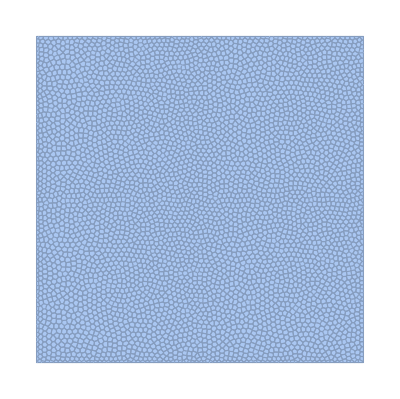

```mathematica
mesh=Import["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\Older Calcium Modeling and Misc\\mesh_4826cells_450x450.m"]
meshRatio=1.;
(*mesh=Import["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\Older Calcium Modeling and Misc\\mesh_100cells_450x450.m"]
meshRatio=.143;(*Just for testing purposes. This ratio takes the 100 cell mesh and changes the lengths to be comparable to the 4826 cell mesh*)*)
```

```mathematica
(*Get information about each cell*)
range=450.;(*From mesh file name (side length of grid in μm)*)

(*Get distances from center of mesh to each cell centroid*)
distances=Sqrt[(#[[1]]-range/2)^2+(#[[2]]-range/2)^2]&/@PropertyValue[{mesh,2},MeshCellCentroid]*meshRatio;
positions=PropertyValue[{mesh,2},MeshCellCentroid];

(*Get number of cells*)
numCells2D=Length@distances;
```

```mathematica
interiorCells=MeshCellIndex[mesh,{2,"Interior"}][[;;,2]];
```

```mathematica
areas=Area[#]&/@MeshPrimitives[mesh,2]*(10^-5)^2*meshRatio^2; (*Convert from μm^2 to dm^2*)
avgArea=Mean[areas[[interiorCells]]];
```

```mathematica
Δx=N[Sqrt[avgArea*(10^5)^2/π]]*2 ;(*Should be around 7.4*)
```

## Make Adjacency Matrix

Create a nPts X nPts matrix that says whether or not a cell is adjacent to another cell. I cannot seem to find a built in function to do this, so I have to code it myself. Instead of making elements either 0 or 1, I make them 0 (not adjacent) or the length of the shared edge. This is because I will assume that the flux of ions/molecules through the gap junctions will be proportional to the length of the shared edge. The larger an edge is shared between cells, the more transfer we would expect due to more gap junctions being present.

```mathematica
(*Determine cells "labels"*)
ablatedPos=Position[distances,x_/;x<ablatedRadius]//Flatten;
woundPos=Position[distances,x_/;ablatedRadius≤x<cavRadMicrons]//Flatten;
highDamagePos=Position[distances,x_/;ablatedRadius≤x<radiusHighDamage]//Flatten;
```

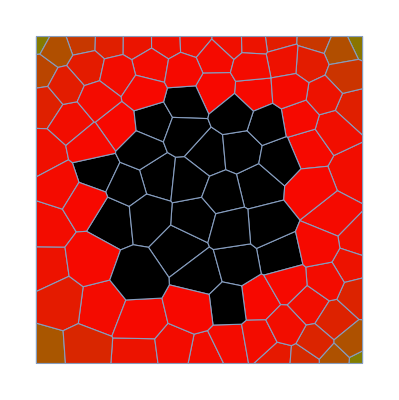

```mathematica
stylesWound=Join[Style[{2,#},Black]&/@ablatedPos,Style[{2,#},RGBColor[μTDist@distances[[#]],1-μTDist@distances[[#]],0.]]&/@woundPos];
Show[HighlightMesh[HighlightMesh[mesh,Style[{2},Green]],stylesWound]]
```

```mathematica
(*Produce adjacency matrix with shared edge lengths as elements*)
Block[{conn,lengths,directions,positionVectors,sines,edges,adj},

(*Get connectivity matrix, which is a matrix whose rows represent a cell and column represents an edge associated with the cell*)
conn=mesh["ConnectivityMatrix"[2,1]]//Unitize//Normal;

(*Lengths of each edge*)
lengths=EuclideanDistance[#[[1]],#[[2]]]&@@@MeshPrimitives[mesh,1];

(*direction vectors of each edge*)
directions=#[[2]]-#[[1]]&@@@MeshPrimitives[mesh,1];

(*position vectors of the midpoints of each edge*)
positionVectors=((#[[1]]+#[[2]])/2-{range/2,range/2})&@@@MeshPrimitives[mesh,1];

(*List of Sin of angle between position vector of edge midpoint (relative to the wound center) and the direciton of the shared edge*)
sines=Table[(Norm@Cross[Append[directions[[i]],0],Append[positionVectors[[i]],0]])/(Norm[directions[[i]]]*Norm[positionVectors[[i]]]),{i,Length@directions}];

(*List where each element is an edge and tells you which cell(s) have that edge*)
edges=(Position[#,1]&/@Transpose[conn])/.{e_}->e;

(*Initialize matrix*)
adj=ConstantArray[0.,{numCells2D,numCells2D}];

(*Function that replaces corresponding elements in the initial adjMat with an edge length if the cells in the row&column share that edge*)
alter[pos_,edge_]:=If[Length[pos]==2,adj[[pos[[1]],pos[[2]]]]=adj[[pos[[2]],pos[[1]]]]=lengths[[edge]]*If[gjPolarize,sines[[edge]],1.]];

MapIndexed[alter[#1,First[#2]]&,edges];

adjMat=SparseArray[adj]*meshRatio;
]
```

```mathematica
(*(*Check to make sure adjacencies are correct*)
Manipulate[HighlightMesh[HighlightMesh[mesh,Join[Thread[{2,Position[Normal[adjMat[[i]]],x_/;x≠0]//Flatten}]]],Style[{2,i},Red]],{i,1,numCells2D,1}]*)
```

## GJ Fluxes

```mathematica
(*random GJ values. Make sure none of them are negative*)
(*randGJmults=If[gjRand,Abs@RandomVariate[NormalDistribution[1.,σGJ],numCells2D],ConstantArray[1.,numCells2D]];*)
randGJmults=If[gjRand,RandomVariate[LogNormalDistribution[-σGJ^2/2,σGJ],numCells2D],ConstantArray[1.,numCells2D]];
```

```mathematica
(*η values are based on a single "ideal" cell of diameter Δx, with flux through its entire perimeter. Therefore, in order to properly scale based on cell volume and shared perimeter between two cells, the GJ fluxes have to be scaled by (v0/Subscript[v, i])*(aij/a0), where the 0 subscript denotes the "ideal" cell, i is the cell in question, and j denotes any cell adjacent to i. Since all cells have the same height, volume ratios are reduced to ratios of PM area, and shared areas are reduced to lengths. So v0 becomes the PM area of the ideal cell, and a0 becomes the circumference of the ideal cell.

a0 and areas are in dm^2, adjMat lengths and Δx are in μm. So the ratios work out to be dimensionless*)
fluxGJCaTerms2D=Table[ηGJc*Total[If[MemberQ[knockoutList,"GJ"]&&(positions[[i,1]]>range/2.||positions[[#,1]]>range/2.),knockoutVal,1.]*If[MemberQ[ablatedPos,i]||MemberQ[ablatedPos,#],connectAblated,1.]*(Min[randGJmults[[i]],randGJmults[[#]]]*(a0/areas[[i]])*(adjMat[[i,#]]/(π*Δx))*(Subscript[c, #][t]-Subscript[c, i][t]))&/@(Flatten@adjMat[[i]]["NonzeroPositions"])],{i,numCells2D}];
fluxIP3Terms2D=Table[ηGJIP3*Total[If[MemberQ[knockoutList,"GJ"]&&(positions[[i,1]]>range/2.||positions[[#,1]]>range/2.),knockoutVal,1.]*If[MemberQ[ablatedPos,i]||MemberQ[ablatedPos,#],connectAblated,1.]*(Min[randGJmults[[i]],randGJmults[[#]]]*(a0/areas[[i]])*(adjMat[[i,#]]/(π*Δx))(Subscript[ip3, #][t]-Subscript[ip3, i][t]))&/@(Flatten@adjMat[[i]]["NonzeroPositions"])],{i,numCells2D}];

(*Unwounded terms; only difference is the part with ablation connection*)
fluxGJCaTerms2DUW=Table[ηGJc*Total[If[MemberQ[knockoutList,"GJ"]&&(positions[[i,1]]>range/2.||positions[[#,1]]>range/2.),knockoutVal,1.]*(Min[randGJmults[[i]],randGJmults[[#]]]*(a0/areas[[i]])*(adjMat[[i,#]]/(π*Δx))*(Subscript[c, #][t]-Subscript[c, i][t]))&/@(Flatten@adjMat[[i]]["NonzeroPositions"])],{i,numCells2D}];
fluxIP3Terms2DUW=Table[ηGJIP3*Total[If[MemberQ[knockoutList,"GJ"]&&(positions[[i,1]]>range/2.||positions[[#,1]]>range/2.),knockoutVal,1.]*(Min[randGJmults[[i]],randGJmults[[#]]]*(a0/areas[[i]])*(adjMat[[i,#]]/(π*Δx))(Subscript[ip3, #][t]-Subscript[ip3, i][t]))&/@(Flatten@adjMat[[i]]["NonzeroPositions"])],{i,numCells2D}];
```

## Making multi-cell equations (equilibrium tissue)

### Randomization Test

This sets up looking at varying parameters across the tissue for testing on ACCRE. This will be done one at a time, but to set this up to be more general I will make it possible to choose any number of parameters. Right now, use the same randomization for each parameter, but this could change in the future.

```mathematica
getRandomCells[numCells_,var_]:=RandomVariate[LogNormalDistribution[-.5*Log[var+1],Sqrt[Log[var+1]]],numCells];

randExtParams={α,ηSERCA};

randVals=Association[Table[randExtParams[[param]]->getRandomCells[numCells2D,.225],{param,Length@randExtParams}]];
```

```mathematica
randRules=Table[(#->#*randVals[[Key@#,cell]])&@randExtParams[[param]],{cell,numCells2D},{param,Length@randExtParams}];
```

### Some set up stuff

```mathematica
gcampRandVals=RandomVariate[LogNormalDistribution[-σgcamp^2/2,σgcamp],numCells2D];
(*plcRandVals=RandomVariate[LogNormalDistribution[-.5*Log[varPLC+1],Sqrt[Log[varPLC+1]]],numCells2D];*)

maxGCAMPVal=Max@gcampRandVals; (*Needed to determine how to scale video output later*)
```

### Single Cell

```mathematica
deqsTissueEQ=deqns/.{rμT->0.,lr->0.};
```

```mathematica
(*Variable replacements for multiple cells*)
depVars2D=Table[Subscript[spec, i][t],{i,numCells2D},{spec,{ip3,h,c,cER}}];
variableReplacements2D=Flatten/@Table[{spec[t]->Subscript[spec, i][t],spec'[t]->Subscript[spec, i]'[t]},{i,numCells2D},{spec,{ip3,h,c,cER}}];
initReplacement2D=Flatten/@Table[{spec[0]->Subscript[spec, i][0]},{i,numCells2D},{spec,{ip3,h,c,cER}}];
```

### Putting it all together

```mathematica
multiCellReplacements2D=
Table[

Join[
variableReplacements2D[[i]],
initReplacement2D[[i]],
{Bx->Bx*If[gcampRand,gcampRandVals[[i]],1.]},
(*{α->α*If[plcRand,plcRandVals[[i]],1.]},*)
(*{α0->α0*If[plcRand,plcRandVals[[i]],1.]},*)
randRules[[i]],
{jGJIP3->fluxIP3Terms2DUW[[i]],jGJc->fluxGJCaTerms2DUW[[i]]},
{r->distances[[i]]}
],

{i,numCells2D}];
```

```mathematica
tissueCellEquationsEQ=deqsTissueEQ/.multiCellReplacements2D;
```

```mathematica
tissueModelEquationsEQ=Flatten[Table[tissueCellEquationsEQ[[i]]/.If[positions[[i,1]]>range/2,knockoutRules,{}]/.If[positions[[i,1]]>range/2,overExpressRules,{}],{i,numCells2D}]]/.intParams;
```

```mathematica
tLong=300.; (*seconds*)
framesBeforeWounding=20;
tissueModelSolEQ=
ParametricNDSolveValue[
tissueModelEquationsEQ,
depVars2D/.Table[{t->τ},{τ,tLong-(framesBeforeWounding-1)*Δt,tLong,Δt}],
{t,0,tLong},
extParams,
DependentVariables->Flatten@depVars2D,
"Method"->{"EquationSimplification"->{Automatic,"TimeConstraint"->100}}];
```

```mathematica
newEQSoln=tissueModelSolEQ@@(finalParamAssociation/@extParams);
```

```mathematica
newEQs=Table[{ip30->#[[i,1]],ca0->#[[i,3]],cER0->#[[i,4]],h0->#[[i,2]]},{i,numCells2D}]&@(Last@newEQSoln);
```

## Full Model (new)

RUN EQUILIBRIUM TISSUE FIRST

### Single Cell

```mathematica
deqsTissue=deqns/.{lr->lrSol[r,t],ip3[0]==x_->ip3[0]==ip30,c[0]==x_->c[0]==ca0,cER[0]==x_->cER[0]==cER0,h[0]==x_->h[0]==h0};
```

```mathematica
(*Making ablated cells have constant calcium. Use Dispatch to make things faster. Might need to modify things other than Calcium*)
ablatedChanges=Dispatch@Flatten@Table[If[MemberQ[ablatedPos,i],{Subscript[c, i]'[t]==x_->Subscript[c, i]'[t]==0,Subscript[c, i][0]==x_->Subscript[c, i][0]==cExt},{Subscript[c, i]'[t]==x_->Subscript[c, i]'[t]==x,Subscript[c, i][0]==x_->Subscript[c, i][0]==x}],{i,numCells2D}];
```

### Putting it all together

```mathematica
(*Comapred to the equilibrium tissue, we add in the new resting levels from the previous section, and we take out the initial condition scaling (since we already have the initial conditions for each cell)*)
multiCellReplacements2D=
Table[

Join[
newEQs[[i]],
variableReplacements2D[[i]],
initReplacement2D[[i]],
{rμT->rμT*μTDist[distances[[i]]]},
{Bx->Bx*If[gcampRand,gcampRandVals[[i]],1.]},
(*{α->α*If[plcRand,plcRandVals[[i]],1.]},*)
(*{α0->α0*If[plcRand,plcRandVals[[i]],1.]},*)
randRules[[i]],
{jGJIP3->fluxIP3Terms2D[[i]],jGJc->fluxGJCaTerms2D[[i]]},
{r->distances[[i]]}
],

{i,numCells2D}];
```

```mathematica
(*Break into separate steps to speed up ablation replacements*)
tissueCellEquations=deqsTissue/.multiCellReplacements2D;

tissueModelEquations=Flatten[Table[tissueCellEquations[[i]]/.If[MemberQ[ablatedPos,i],{Subscript[c, i]'[t]==x_->Subscript[c, i]'[t]==0,Subscript[c, i][0]==x_->Subscript[c, i][0]==cExt},{}]/.If[positions[[i,1]]>range/2,knockoutRules,{}]/.If[positions[[i,1]]>range/2,overExpressRules,{}],{i,numCells2D}]]/.intParams;
```

```mathematica
tissueModelSol=
ParametricNDSolveValue[
tissueModelEquations,
depVars2D[[;;,3]],
{t,0,400.},
extParams,
DependentVariables->Flatten@depVars2D,
"Method"->{"EquationSimplification"->{Automatic,"TimeConstraint"->100}}];
```

```mathematica
test=tissueModelSol@@(finalParamAssociation/@extParams);
```

```mathematica
testG=CtoF/@test;
```

### Animation

```mathematica
(*Set frames before wounding to be resting calcium levels*)
```

```mathematica
animate2D[soln_]:=
Block[{timePoints,minF,maxF,styles,animList,frames},
timePoints=Join[CtoF@(newEQSoln[[;;,;;,3]]),Table[soln[[i]]/.t->τ,{τ,0.1,400.1,Δt},{i,numCells2D}]];

minF=.12;
maxF=1.;

styles=
Table[Style[{2,i},If[MemberQ[ablatedPos,i]&&τ>framesBeforeWounding,Black,GrayLevel[Min[maxF,If[gcampRand,gcampRandVals[[i]],1.]*Rescale[timePoints[[τ,i]],{minInt,maxInt*maxGCAMPVal},{minF,maxF}]]]]],{τ,Length@timePoints},{i,numCells2D}];

animList=HighlightMesh[mesh,#,MeshCellStyle->{1->Directive[Opacity[0],Antialiasing->False]}]&/@styles;

frames=MapIndexed[Show[#1,Graphics[{White,Text[Style["t = "<>ToString[Round[Δt*(First[#2]-(framesBeforeWounding+1)),.1]]<>" s",White,18],{75,35}],White,Thickness@.025,Line[{{.75*range,.1*range},{.75*range+50,.1*range}}]}]]&,animList];

Return[frames]

(*ListAnimate[frames,7]*)
]
```

```mathematica
frames2D=animate2D[testG];
```

```mathematica
ListAnimate[frames2D,7]
```

```mathematica
(*FREE CALCIUM*)
animate2Dcalc[soln_]:=
Block[{timePoints,minF,maxF,styles,animList,frames},
timePoints=Join[newEQSoln[[;;,;;,3]],Table[soln[[i]]/.t->τ,{τ,0.1,400.1,Δt},{i,numCells2D}]];

styles=Table[Style[{2,i},If[MemberQ[ablatedPos,i]&&τ>framesBeforeWounding,Black,HotColor[Rescale[timePoints[[τ,i]],{0.0884695559645682,1.4/2}]]]],{τ,Length@timePoints},{i,numCells2D}];

animList=HighlightMesh[mesh,#,MeshCellStyle->{1->Directive[Opacity[0],Antialiasing->False]}]&/@styles;
frames=MapIndexed[
Show[#1,Graphics[{White,Text[Style["t = "<>ToString[Round[Δt*(First[#2]-11),.1]]<>" s",White,18],{75,35}],White,Thickness@.025,Line[{{.75*range,.1*range},{.75*range+50,.1*range}}]}]]&,animList];

Return[frames]
(*ListAnimate[frames,7]*)]
frames2Dcalc=animate2Dcalc[test];
```

```mathematica
(*FREE CALCIUM OLD*)
animate2Dcalc[soln_]:=
Block[{timePoints,minF,maxF,styles,animList,frames},
timePoints=Table[soln[[i]]/.t->τ,{τ,0.1,400.1,Δt},{i,numCells2D}];
styles=Join[
Table[Style[{2,i},HotColor[Rescale[newEQSoln[[i,3]],{0.0884695559645682,1.4/2}]]],10,{i,numCells2D}],
Table[Style[{2,i},If[MemberQ[ablatedPos,i],Black,HotColor[Rescale[timePoints[[τ,i]],{0.0884695559645682,1.4/2}]]]],{τ,Length@timePoints},{i,numCells2D}]
];
animList=HighlightMesh[mesh,#,MeshCellStyle->{1->Directive[Opacity[0],Antialiasing->False]}]&/@styles;
frames=MapIndexed[
Show[#1,Graphics[{White,Text[Style["t = "<>ToString[Round[Δt*(First[#2]-11),.1]]<>" s",White,18],{75,35}],White,Thickness@.025,Line[{{.75*range,.1*range},{.75*range+50,.1*range}}]}]]&,animList];

Return[frames]
(*ListAnimate[frames,7]*)]
frames2Dcalc=animate2Dcalc[test];
```

# Jump The Gap

Originally copied from final model section above, so some comments might not apply or make sense

Final code for testing a parameter set chosen above. This code is tested using the “zoomed in mesh”, but the goal is to move this to ACCRE to run on the full mesh. Ideally only the Initialization section as well as this section are the only things that will need to go to ACCRE; the other sections should be removed when making the ACCRE notebook, as they are just for the purpose of testing the parameters.

```mathematica
(*finalParamAssociation=<|rμT->41.14497773461118,τHeal->5.25,rPMCA->0.12,kPMCA->0.1,rSOC->0.15000000000000002,ηNCX->10.,nNCX->2.5,kNCX->1.6,rlkPM->0.00025,α->0.9,α0->0.1,kl->0.05,nl->5.,Kc->0.4,ηIPR->4.,ηSERCA->5.,kSERCA1->0.1,kSERCA2->0.,ηlkER->0.01,Bx->5.,ηGJIP3->4.,ηGJc->2.,connectAblated->0.025|>

FINAL PARAMETER DEFINED IN FINAL MODEL SECTION. So I am not splitting up where the parameters are being set*)
```

## Initializations

```mathematica
(*List of strings to specify model components to knockout by 70% in one half of the tissue. Current options are GJ, PLC, SERCA, SOC, PMCA. Note that GJs are handled separately when GJ terms are made, since the GJ parameters are specific to cell-cell boundaries rather than single cells.*)
knockoutVal=.3(*percentage to keep for knockout (so 1 - this for percent knockdown)*);
knockoutList={"PLC"};

(*knockout commands that do not require user input*)
knockoutAssociations=
<|"GJ"->Nothing,
"PLC"->({α->#*α(*,α0->#*α0*)}),
"SERCA"->(ηSERCA->#*ηSERCA),
"SOC"->(ηSOC->#*ηSOC),
"PMCA"->(ηPMCA->#*ηPMCA)|>&@knockoutVal;

knockoutRules=Flatten[knockoutAssociations/@knockoutList];
```

```mathematica
gjRand=True; (*True = give each cell a random GJ parameter the tissue model. Value for a border determined by smallest value of the two cells that share that border*)
σGJ=.4;(*σ parameter for GJ randomness*)
gjPolarize=False; (*True = multiply GJ params by sinθ, where θ is the angle between the radial vector to a cell edge and the direction of the cell edge*)

gcampRand=True; (*True = randomize the amount of GCaMP in each cell. The random scale will also scale the fluorescence values of the model output*)
σgcamp=.1;(*σ parameter for gcamp randomizer*)

plcRand=True; (*True = randomize PLC (parameter α) between cells*)
varPLC=.225; (*standard deviation for PLC randomizer*)

(*connectAblated=0.015; (*parameter to connect the ablated region to the rest of the tissue. The range can be 1 (full connection) to 0 (no connection)*)*)
connectAblated=.;
```

## Mesh

```mathematica
(*mesh=Import["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\Older Calcium Modeling and Misc\\mesh_4826cells_450x450.m"]
meshRatio=1.;*)
mesh=Import["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\Older Calcium Modeling and Misc\\mesh_100cells_450x450.m"]
meshRatio=.143;(*Just for testing purposes. This ratio takes the 100 cell mesh and changes the lengths to be comparable to the 4826 cell mesh*)
```

-Graphics-

```mathematica
(*Get information about each cell*)
range=450.;(*From mesh file name (side length of grid in μm)*)

(*Get distances from center of mesh to each cell centroid*)
distances=Sqrt[(#[[1]]-range/3)^2+(#[[2]]-2*range/3)^2]&/@PropertyValue[{mesh,2},MeshCellCentroid]*meshRatio;
positions=PropertyValue[{mesh,2},MeshCellCentroid];

(*Get number of cells*)
numCells2D=Length@distances;
```

```mathematica
interiorCells=MeshCellIndex[mesh,{2,"Interior"}][[;;,2]];
```

```mathematica
areas=Area[#]&/@MeshPrimitives[mesh,2]*(10^-5)^2*meshRatio^2; (*Convert from μm^2 to dm^2*)
avgArea=Mean[areas[[interiorCells]]];
```

```mathematica
Δx=N[Sqrt[avgArea*(10^5)^2/π]]*2 ;(*Should be around 7.4*)
```

## Make Adjacency Matrix

Create a nPts X nPts matrix that says whether or not a cell is adjacent to another cell. I cannot seem to find a built in function to do this, so I have to code it myself. Instead of making elements either 0 or 1, I make them 0 (not adjacent) or the length of the shared edge. This is because I will assume that the flux of ions/molecules through the gap junctions will be proportional to the length of the shared edge. The larger an edge is shared between cells, the more transfer we would expect due to more gap junctions being present.

```mathematica
(*Determine cells "labels"*)
ablatedPos=Position[distances,x_/;x<ablatedRadius]//Flatten;
woundPos=Position[distances,x_/;ablatedRadius≤x<cavRadMicrons]//Flatten;
highDamagePos=Position[distances,x_/;ablatedRadius≤x<radiusHighDamage]//Flatten;
```

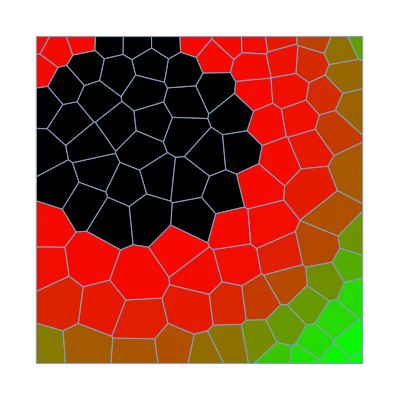

```mathematica
stylesWound=Join[Style[{2,#},Black]&/@ablatedPos,Style[{2,#},RGBColor[μTDist@distances[[#]],1-μTDist@distances[[#]],0.]]&/@woundPos];
Show[HighlightMesh[HighlightMesh[mesh,Style[{2},Green]],stylesWound]]
```

```mathematica
(*Produce adjacency matrix with shared edge lengths as elements*)
Block[{conn,lengths,directions,positionVectors,sines,edges,adj},

(*Get connectivity matrix, which is a matrix whose rows represent a cell and column represents an edge associated with the cell*)
conn=mesh["ConnectivityMatrix"[2,1]]//Unitize//Normal;

(*Lengths of each edge*)
lengths=EuclideanDistance[#[[1]],#[[2]]]&@@@MeshPrimitives[mesh,1];

(*direction vectors of each edge*)
directions=#[[2]]-#[[1]]&@@@MeshPrimitives[mesh,1];

(*position vectors of the midpoints of each edge*)
positionVectors=((#[[1]]+#[[2]])/2-{range/2,range/2})&@@@MeshPrimitives[mesh,1];

(*List of Sin of angle between position vector of edge midpoint (relative to the wound center) and the direciton of the shared edge*)
sines=Table[(Norm@Cross[Append[directions[[i]],0],Append[positionVectors[[i]],0]])/(Norm[directions[[i]]]*Norm[positionVectors[[i]]]),{i,Length@directions}];

(*List where each element is an edge and tells you which cell(s) have that edge*)
edges=(Position[#,1]&/@Transpose[conn])/.{e_}->e;

(*Initialize matrix*)
adj=ConstantArray[0.,{numCells2D,numCells2D}];

(*Function that replaces corresponding elements in the initial adjMat with an edge length if the cells in the row&column share that edge*)
alter[pos_,edge_]:=If[Length[pos]==2,adj[[pos[[1]],pos[[2]]]]=adj[[pos[[2]],pos[[1]]]]=lengths[[edge]]*If[gjPolarize,sines[[edge]],1.]];

MapIndexed[alter[#1,First[#2]]&,edges];

adjMat=SparseArray[adj]*meshRatio;
]
```

```mathematica
(*(*Check to make sure adjacencies are correct*)
Manipulate[HighlightMesh[HighlightMesh[mesh,Join[Thread[{2,Position[Normal[adjMat[[i]]],x_/;x≠0]//Flatten}]]],Style[{2,i},Red]],{i,1,numCells2D,1}]*)
```

## GJ Fluxes

```mathematica
(*random GJ values. Make sure none of them are negative*)
(*randGJmults=If[gjRand,Abs@RandomVariate[NormalDistribution[1.,σGJ],numCells2D],ConstantArray[1.,numCells2D]];*)
randGJmults=If[gjRand,RandomVariate[LogNormalDistribution[-σGJ^2/2,σGJ],numCells2D],ConstantArray[1.,numCells2D]];
```

```mathematica
(*η values are based on a single "ideal" cell of diameter Δx, with flux through its entire perimeter. Therefore, in order to properly scale based on cell volume and shared perimeter between two cells, the GJ fluxes have to be scaled by (v0/Subscript[v, i])*(aij/a0), where the 0 subscript denotes the "ideal" cell, i is the cell in question, and j denotes any cell adjacent to i. Since all cells have the same height, volume ratios are reduced to ratios of PM area, and shared areas are reduced to lengths. So v0 becomes the PM area of the ideal cell, and a0 becomes the circumference of the ideal cell.

a0 and areas are in dm^2, adjMat lengths and Δx are in μm. So the ratios work out to be dimensionless*)
fluxGJCaTerms2D=Table[ηGJc*Total[If[MemberQ[knockoutList,"GJ"]&&(positions[[i,1]]>range/2.||positions[[#,1]]>range/2.),knockoutVal,1.]*If[MemberQ[ablatedPos,i]||MemberQ[ablatedPos,#],connectAblated,1.]*(Min[randGJmults[[i]],randGJmults[[#]]]*(a0/areas[[i]])*(adjMat[[i,#]]/(π*Δx))*(Subscript[c, #][t]-Subscript[c, i][t]))&/@(Flatten@adjMat[[i]]["NonzeroPositions"])],{i,numCells2D}];
fluxIP3Terms2D=Table[ηGJIP3*Total[If[MemberQ[knockoutList,"GJ"]&&(positions[[i,1]]>range/2.||positions[[#,1]]>range/2.),knockoutVal,1.]*If[MemberQ[ablatedPos,i]||MemberQ[ablatedPos,#],connectAblated,1.]*(Min[randGJmults[[i]],randGJmults[[#]]]*(a0/areas[[i]])*(adjMat[[i,#]]/(π*Δx))(Subscript[ip3, #][t]-Subscript[ip3, i][t]))&/@(Flatten@adjMat[[i]]["NonzeroPositions"])],{i,numCells2D}];

(*Unwounded terms; only difference is the part with ablation connection*)
fluxGJCaTerms2DUW=Table[ηGJc*Total[If[MemberQ[knockoutList,"GJ"]&&(positions[[i,1]]>range/2.||positions[[#,1]]>range/2.),knockoutVal,1.]*(Min[randGJmults[[i]],randGJmults[[#]]]*(a0/areas[[i]])*(adjMat[[i,#]]/(π*Δx))*(Subscript[c, #][t]-Subscript[c, i][t]))&/@(Flatten@adjMat[[i]]["NonzeroPositions"])],{i,numCells2D}];
fluxIP3Terms2DUW=Table[ηGJIP3*Total[If[MemberQ[knockoutList,"GJ"]&&(positions[[i,1]]>range/2.||positions[[#,1]]>range/2.),knockoutVal,1.]*(Min[randGJmults[[i]],randGJmults[[#]]]*(a0/areas[[i]])*(adjMat[[i,#]]/(π*Δx))(Subscript[ip3, #][t]-Subscript[ip3, i][t]))&/@(Flatten@adjMat[[i]]["NonzeroPositions"])],{i,numCells2D}];
```

## Making multi-cell equations (equilibrium tissue)

### Some set up stuff

```mathematica
(*gcampRandVals=Abs@RandomVariate[NormalDistribution[1.,σgcamp],numCells2D];
plcRandVals=Abs@RandomVariate[NormalDistribution[1.,σPLC],numCells2D];*)

gcampRandVals=RandomVariate[LogNormalDistribution[-σgcamp^2/2,σgcamp],numCells2D];
plcRandVals=RandomVariate[LogNormalDistribution[-.5*Log[varPLC+1],Sqrt[Log[varPLC+1]]],numCells2D];

maxGCAMPVal=Max@gcampRandVals; (*Needed to determine how to scale video output later*)
```

### Single Cell

```mathematica
deqsTissueEQ=deqns/.{rμT->0.,lr->0.};
```

```mathematica
(*Variable replacements for multiple cells*)
depVars2D=Table[Subscript[spec, i][t],{i,numCells2D},{spec,{ip3,h,c,cER}}];
variableReplacements2D=Flatten/@Table[{spec[t]->Subscript[spec, i][t],spec'[t]->Subscript[spec, i]'[t]},{i,numCells2D},{spec,{ip3,h,c,cER}}];
initReplacement2D=Flatten/@Table[{spec[0]->Subscript[spec, i][0]},{i,numCells2D},{spec,{ip3,h,c,cER}}];
```

### Putting it all together

```mathematica
multiCellReplacements2D=
Table[

Join[
variableReplacements2D[[i]],
initReplacement2D[[i]],
{Bx->Bx*If[gcampRand,gcampRandVals[[i]],1.]},
{α->α*If[plcRand,plcRandVals[[i]],1.]},
(*{α0->α0*If[plcRand,plcRandVals[[i]],1.]},*)
{jGJIP3->fluxIP3Terms2DUW[[i]],jGJc->fluxGJCaTerms2DUW[[i]]},
{r->distances[[i]]}
],

{i,numCells2D}];
```

```mathematica
tissueCellEquationsEQ=deqsTissueEQ/.multiCellReplacements2D;
```

```mathematica
tissueModelEquationsEQ=Flatten[Table[tissueCellEquationsEQ[[i]]/.If[positions[[i,1]]<positions[[i,2]],knockoutRules,{}],{i,numCells2D}]]/.intParams;
```

```mathematica
tLong=6000.; (*seconds*)
tissueModelSolEQ=
ParametricNDSolveValue[
tissueModelEquationsEQ,
depVars2D/.t->tLong,
{t,0,tLong},
extParams,
DependentVariables->Flatten@depVars2D,
"Method"->{"EquationSimplification"->{Automatic,"TimeConstraint"->100}}];
```

```mathematica
newEQSoln=tissueModelSolEQ@@(finalParamAssociation/@extParams);
```

```mathematica
newEQs=Table[{ip30->#[[i,1]],ca0->#[[i,3]],cER0->#[[i,4]],h0->#[[i,2]]},{i,numCells2D}]&@newEQSoln;
```

## Full Model (new)

RUN EQUILIBRIUM TISSUE FIRST

### Single Cell

```mathematica
deqsTissue=deqns/.{lr->lrSol[r,t],ip3[0]==x_->ip3[0]==ip30,c[0]==x_->c[0]==ca0,cER[0]==x_->cER[0]==cER0,h[0]==x_->h[0]==h0};
```

```mathematica
(*Making ablated cells have constant calcium. Use Dispatch to make things faster. Might need to modify things other than Calcium*)
ablatedChanges=Dispatch@Flatten@Table[If[MemberQ[ablatedPos,i],{Subscript[c, i]'[t]==x_->Subscript[c, i]'[t]==0,Subscript[c, i][0]==x_->Subscript[c, i][0]==cExt},{Subscript[c, i]'[t]==x_->Subscript[c, i]'[t]==x,Subscript[c, i][0]==x_->Subscript[c, i][0]==x}],{i,numCells2D}];
```

### Putting it all together

```mathematica
(*Comapred to the equilibrium tissue, we add in the new resting levels from the previous section, and we take out the initial condition scaling (since we already have the initial conditions for each cell)*)
multiCellReplacements2D=
Table[

Join[
newEQs[[i]],
variableReplacements2D[[i]],
initReplacement2D[[i]],
{rμT->rμT*μTDist[distances[[i]]]},
{Bx->Bx*If[gcampRand,gcampRandVals[[i]],1.]},
{α->α*If[plcRand,plcRandVals[[i]],1.]},
(*{α0->α0*If[plcRand,plcRandVals[[i]],1.]},*)
{jGJIP3->fluxIP3Terms2D[[i]],jGJc->fluxGJCaTerms2D[[i]]},
{r->distances[[i]]}
],

{i,numCells2D}];
```

```mathematica
(*Break into separate steps to speed up ablation replacements*)
tissueCellEquations=deqsTissue/.multiCellReplacements2D;

tissueModelEquations=Flatten[Table[tissueCellEquations[[i]]/.If[MemberQ[ablatedPos,i],{Subscript[c, i]'[t]==x_->Subscript[c, i]'[t]==0,Subscript[c, i][0]==x_->Subscript[c, i][0]==cExt},{}]/.If[positions[[i,1]]<positions[[i,2]],knockoutRules,{}],{i,numCells2D}]]/.intParams;
```

```mathematica
tissueModelSol=
ParametricNDSolveValue[
tissueModelEquations,
depVars2D[[;;,3]],
{t,0,400.},
extParams,
DependentVariables->Flatten@depVars2D,
"Method"->{"EquationSimplification"->{Automatic,"TimeConstraint"->100}}];
```

```mathematica
test=tissueModelSol@@(finalParamAssociation/@extParams);
```

```mathematica
testG=CtoF/@test;
```

### Animation

```mathematica
(*Set frames before wounding to be resting calcium levels*)
```

```mathematica
animate2D[soln_]:=
Block[{timePoints,minF,maxF,styles,animList,frames},
timePoints=Table[soln[[i]]/.t->τ,{τ,0.1,400.1,Δt},{i,numCells2D}];

minF=.12;
maxF=1.;

styles=
Join[
Table[Style[{2,i},GrayLevel[Min[maxF,If[gcampRand,gcampRandVals[[i]],1.]*Rescale[CtoF[newEQSoln[[i,3]]],{minInt,maxInt*maxGCAMPVal},{minF,maxF}]]]],10,{i,numCells2D}],

Table[Style[{2,i},If[MemberQ[ablatedPos,i],Black,GrayLevel[Min[maxF,If[gcampRand,gcampRandVals[[i]],1.]*Rescale[timePoints[[τ,i]],{minInt,maxInt*maxGCAMPVal},{minF,maxF}]]]]],{τ,Length@timePoints},{i,numCells2D}]
];

animList=HighlightMesh[mesh,#,MeshCellStyle->{1->Directive[Opacity[0],Antialiasing->False]}]&/@styles;

frames=MapIndexed[Show[#1,Graphics[{White,Text[Style["t = "<>ToString[Round[Δt*(First[#2]-11.),.1]]<>" s",White,18],{75,35}],Yellow,Line[{{0,0},{range,range}}],White,Thickness@.025,Line[{{.75*range,.1*range}{.75*range+50,.1*range}}]}]]&,animList];

Return[frames]

(*ListAnimate[frames,7]*)
]
```

```mathematica
frames2D=animate2D[testG];
```

```mathematica
ListAnimate[frames2D,7]
```

# Old Cells

## Old Manipulate that uses sliders rather than direct value entry

```mathematica
Manipulate[
Block[
{paramAssociation,
healTimeContour
},

paramAssociation=
Association@{rμT->rμTP,τHeal->τHealP,rPMCA->rPMCAP,kPMCA->kPMCAP,rSOC->rSOCP,ηNCX->ηNCXP,kNCX->kNCXP,rlkPM->rlkPMP,α->0.,α0->α0P,kl->klP,nl->nlP,Kc->KcP,ηIPR->ηIPRP,ηSERCA->ηSERCAP,kSERCA->kSERCAP,ηlkER->ηlkERP,Bx->BxP};

If[updateContour,
getHealContour[paramAssociation,100.,{4.5,10.,.5},{.02,.14,.02}][[2]],
"Contour has not been generated"
]

]
,
Row[{

Column@{
Style["Model Parameters",16,Bold],
Control@{{rμTP,5.},.1,10.,.1},
Control@{{τHealP,5.},1.,100.,1.},
Control@{{rPMCAP,.1},.01,1.,.01},
Control@{{kPMCAP,.1},.01,10.,.01},
Control@{{rSOCP,.1},.01,10.,.01},
Control@{{ηNCXP,50.},1.,100.,1.},
Control@{{kNCXP,8.},.1,10.,.1},
Control@{{rlkPMP,.04},.001,.1,.001},
Control@{{αP,2.},.01,10.,.01},
Control@{{α0P,.1},.01,1.,.01},
Control@{{klP,.05},0.,1.,.01},
Control@{{nlP,3.},1.,10.,1.},
Control@{{KcP,.4},.1,1.,.1},
Control@{{ηIPRP,24.1},.1,100.,.1},
Control@{{ηSERCAP,20.1},.1,100.,.1},
Control@{{kSERCAP,.1},.01,10.,.01},
Control@{{ηlkERP,.03},.001,.1,.001},
Control@{{BxP,5.},.1,10.,.1}
},

Dynamic@
Column@{
Style["Heal Contour Settings",16,Bold],
Control@{{updateContour,False},{False,True}},
Control@{{τMin,4.5},1.,100.,.5},
Control@{{τMax,10.},1.,100.,5.},
Control@{{τStep,.5},.1,1.,.1},
Control@{{rμTMin,.02},.01,1.,.01},
Control@{{rμTMax,.14},.01,1.,.01},
Control@{{rμTStep,.02},.01,.1,.01}
}
}],

SynchronousUpdating->False]
```

## Old Manipulate where each test was a different column

```mathematica
(*Initializations*)
contourInfo="Contour has not been generated";
updateContour=False;

info1D="1D Model hsa not been updated";
update1D=False;

info2D="2D Model hsa not been updated";
update2D=False;

Manipulate[
Block[
{paramAssociation
},

(*rμT value is irrelevant before contour is set*)
paramAssociation=
Association@{rμT->If[!(contourInfo==="Contour has not been generated"),contourInfo[[1]][τHealP]/μTConversion,5.],τHeal->τHealP,rPMCA->rPMCAP,kPMCA->kPMCAP,rSOC->rSOCP,ηNCX->ηNCXP,kNCX->kNCXP,rlkPM->rlkPMP,α->αP,α0->α0P,kl->klP,nl->nlP,Kc->KcP,ηIPR->ηIPRP,ηSERCA->ηSERCAP,kSERCA->kSERCAP,ηlkER->ηlkERP,Bx->BxP,ηGJIP3->ηGJIP3P,ηGJc->ηGJcP};

(*Update heal contour for τHeal and rμT. Update rμT*)
If[updateContour,
(*if update contour*)
contourInfo=getHealContour[ReplacePart[paramAssociation,Key@α->0.],maxTimeRangeDKO,{τMin,τMax,τStep},{rμTMin,rμTMax,rμTStep}]; 
updateContour=False;
paramAssociation=
Association@{rμT->contourInfo[[1]][τHealP]/μTConversion,τHeal->τHealP,rPMCA->rPMCAP,kPMCA->kPMCAP,rSOC->rSOCP,ηNCX->ηNCXP,kNCX->kNCXP,rlkPM->rlkPMP,α->αP,α0->α0P,kl->klP,nl->nlP,Kc->KcP,ηIPR->ηIPRP,ηSERCA->ηSERCAP,kSERCA->kSERCAP,ηlkER->ηlkERP,Bx->BxP,ηGJIP3->ηgGJP3P,ηGJc->ηGJcP};,

(*If not update contour*)
"Contour has not been generated"
];

(*Update 1D model*)
If[update1D,
info1D=get1DSol[ReplacePart[paramAssociation,Key@α->0.],maxTimeRange1D];
update1D=False;,

"1D Model is not Updated"];

(*Update 2D model*)
If[update2D,
info2D=getIP3SpikeSol[ReplacePart[paramAssociation,{Key@α->plcScale*paramAssociation[α],Key@rμT->0.}],maxTimeRange2D,ip3SpikeScale];
update2D=False;,

"2D Model is not Updated"];



(*Main Display Switch*)
Switch[mainView,

(*Display of the heal contour*)
"Heal Contour",
If[!(contourInfo==="Contour has not been generated"),
Switch[contourView,
"25 s",
Show[contourInfo[[3]],Graphics[{Red,PointSize@Large,Point[{τHealP,contourInfo[[1]][τHealP]}]}]],

"All",
contourInfo[[2]]],

contourInfo],

(*Display of 1D model*)
"1D model",
If[!(info1D==="1D Model hsa not been updated"),
Switch[view1D,
"Ca^(2+) Rad",
info1D[[2]],

"GCaMP",
Manipulate[
info1D[[1,ring]],
{ring,1,Length@info1D[[1]],1}]
],

info1D

],

(*Display of IP3 Spike*)
"IP3 Spike",
If[!(info2D==="2D Model hsa not been updated"),
Manipulate[info2D[[1,i]],{i,1,Length@info2D[[1]],1}]
,
info2D
],

(*Display of the full single cell model*)
"Single-Cell",
"TBF"
]

]
,

Row[{

Column@{
Control@{mainView,{"Heal Contour","1D model","IP3 Spike","Single-Cell"}},
Style["Model Parameters",16,Bold],
Control@{τHealP,7.5},
Control@{rPMCAP,.1},
Control@{kPMCAP,.1},
Control@{rSOCP,.1},
Control@{ηNCXP,50.},
Control@{kNCXP,8.},
Control@{rlkPMP,.04},
Control@{αP,2.},
Control@{α0P,.1},
Control@{klP,.05},
Control@{nlP,3.},
Control@{KcP,.4},
Control@{ηIPRP,24.1},
Control@{ηSERCAP,20.1},
Control@{kSERCAP,.1},
Control@{ηlkERP,.03},
Control@{BxP,5.},
Control@{ηGJIP3P,.5},
Control@{ηGJcP,10.}
},

Column@{
Style["Heal Contour Settings",16,Bold],
Button["Update Contour",updateContour=True;],
Control@{maxTimeRangeDKO,100.},
Control@{τMin,4.5},
Control@{τMax,10.},
Control@{τStep,.5},
Control@{rμTMin,.5},
Control@{rμTMax,2.5},
Control@{rμTStep,.5},
Control@{contourView,{"25 s","All"}}
},

Column@{
Style["Radial Cell Line Settings",16,Bold],
Button["Update 1D Model",update1D=True;],
Control@{maxTimeRange1D,400.},
Control@{view1D,{"Ca^(2+) Rad","GCaMP"}}
},

Column@{
Style["IP3 Spike Settings",16,Bold],
Button["Update Ip3 Spike Model",update2D=True;],
Control@{maxTimeRange2D,400.},
Control@{plcScale,1.},
Control@{ip3SpikeScale,1000.}
}
}],

SynchronousUpdating->False]
```

## Old single cell function

```mathematica
getSingleCellSol//ClearAll
getSingleCellSol[
paramAssociation_?AssociationQ,
maxTime_?NumberQ,
dist_?NumberQ]:=
Block[
{params=Prepend[paramAssociation/@extParams,dist],
solution=
ParametricNDSolveValue[modelEqnsSingleCell,{ip3[t],c[t],cER[t],h[t],CtoF[c[t]],Append[fluxes,Total@fluxes]},{t,0,maxTime},Prepend[extParams,r],DependentVariables->{ip3[t],c[t],cER[t],h[t]}],

singleCellOutput
},

singleCellOutput=solution@@params;

Return[
{
Plot[singleCellOutput[[5]],{t,0,maxTime},PlotRange->{.9*minInt,1.1*maxInt},AxesLabel->{"t (s)","GCaMP Fl"},
Epilog->
{Gray,
Line[{{35,.9*minInt},{35,1.1*maxInt}}],
Line[{{140,.9*minInt},{140,1.1*maxInt}}],
Line[{{0,Mean[{minInt,maxInt}]},{1000,Mean[{minInt,maxInt}]}}],

Black,
Text["None",{20,1.05*maxInt}],
Text["Second Exp.",{80,1.05*maxInt}],
Text["Flares",{230,1.05*maxInt}]
}],
Plot[singleCellOutput[[2]],{t,0,maxTime},PlotRange->All,AxesLabel->{"t (s)","[Ca^(2+)] (μM)"}],
Plot[singleCellOutput[[3]],{t,0,maxTime},PlotRange->All,AxesLabel->{"t (s)","[Ca^(2+)]_ER (μM)"}],
Plot[singleCellOutput[[1]],{t,0,maxTime},PlotRange->All,AxesLabel->{"t (s)","[IP_3] (μM)"}],
Plot[singleCellOutput[[4]],{t,0,maxTime},PlotRange->All,AxesLabel->{"t (s)","h"}],
Plot[Evaluate@singleCellOutput[[6]],{t,0,maxTime},PlotRange->All,AxesLabel->{"t (s)","GCaMP Fl"},
PlotLegends->{"jIPR","jSERCA","jlkER","jSOC","jPMCA","jNCX","jlkPM","jμT","jTotal"}]
}
];

]
```

## Saved Parameters

```mathematica
Control@{τHealP,7.5},
Control@{rPMCAP,.1},
Control@{kPMCAP,.1},
Control@{rSOCP,.1},
Control@{ηNCXP,50.},
Control@{kNCXP,8.},
Control@{rlkPMP,.04},
Control@{αP,2.},
Control@{α0P,.1},
Control@{klP,.05},
Control@{nlP,3.},
Control@{KcP,.4},
Control@{ηIPRP,24.1},
Control@{ηSERCAP,20.1},
Control@{kSERCAP,.1},
Control@{ηlkERP,.03},
Control@{BxP,5.},
Control@{ηGJIP3P,.5},
Control@{ηGJcP,10.}
```

```mathematica
Control@{τHealP,100.},
Control@{rPMCAP,.1},
Control@{kPMCAP,.1},
Control@{rSOCP,.1},
Control@{ηNCXP,50.},
Control@{kNCXP,8.},
Control@{rlkPMP,.0002},
Control@{αP,2.},
Control@{α0P,.1},
Control@{klP,.05},
Control@{nlP,3.},
Control@{KcP,.4},
Control@{ηIPRP,24.1},
Control@{ηSERCAP,20.1},
Control@{kSERCAP,.1},
Control@{ηlkERP,.03},
Control@{BxP,5.},
Control@{ηGJIP3P,.5},
Control@{ηGJcP,10.}
```

```mathematica
(*testing*)
```

```mathematica
Column@{
Control@{mainView,{"Heal Contour","1D model","IP3 Spike","Single-Cell"}},
Style["Model Parameters",16,Bold],
Control@{τHealP,7.5},
Control@{rPMCAP,.1},
Control@{kPMCAP,.1},
Control@{rSOCP,.1},
Control@{ηNCXP,50.},
Control@{kNCXP,8.},
Control@{rlkPMP,.04},
Control@{αP,2.},
Control@{α0P,.1},
Control@{klP,.05},
Control@{nlP,3.},
Control@{KcP,.4},
Control@{ηIPRP,24.1},
Control@{ηSERCAP,20.1},
Control@{kSERCAP,.1},
Control@{ηlkERP,.03},
Control@{BxP,5.},
Control@{ηGJIP3P,.5},
Control@{ηGJcP,10.}
},
```

# Test Cells

```mathematica
{ημT,τHeal,α,α0,Kc,ηIPR,ηSERCA,kSERCA,ηlkER,ηPMCA,kPMCA,ηSOC,ηNCX,kNCX,ηlkPM,Bx,kl,nl};
{0.25,10.,0,0.1,0.4,24.1,20.1,0.1,0.03,5.,0.1,5.2565,50.,8.,0.00001,5.,0.05,3.}
```

```mathematica
{rμT,τHeal,ηNCX,kNCX,rPMCA,kPMCA,rlkPM,Bx};
```

```mathematica
contourPoints
```

{{1.,0.25,fail},{1.,0.375,fail},{1.,0.5,1.41646},{1.,0.625,1.86583},{1.,0.75,2.24948},{1.,0.875,2.6002},{1.,1.,2.92577},{1.,1.125,3.22882},{1.,1.25,3.51163},{1.,1.375,3.77651},{1.,1.5,4.02561},{1.,1.625,4.26088},{1.,1.75,4.48398},{1.,1.875,4.69634},{1.,2.,4.89918},{1.,2.125,5.09355},{1.,2.25,5.28035},{1.,2.375,5.46034},{1.,2.5,5.63421},{1.5,0.25,fail},{1.5,0.375,1.32632},{1.5,0.5,2.16117},{1.5,0.625,2.81002},{1.5,0.75,3.38647},{1.5,0.875,3.90789},{1.5,1.,4.38001},{1.5,1.125,4.80915},{1.5,1.25,5.20169},{1.5,1.375,5.56328},{1.5,1.5,5.89867},{1.5,1.625,6.21175},{1.5,1.75,6.5057},{1.5,1.875,6.78313},{1.5,2.,7.04622},{1.5,2.125,7.29679},{1.5,2.25,7.53636},{1.5,2.375,7.76627},{1.5,2.5,7.98763},{2.,0.25,fail},{2.,0.375,1.86576},{2.,0.5,2.94082},{2.,0.625,3.83945},{2.,0.75,4.63173},{2.,0.875,5.32974},{2.,1.,5.94711},{2.,1.125,6.49817},{2.,1.25,6.99519},{2.,1.375,7.44794},{2.,1.5,7.86409},{2.,1.625,8.24966},{2.,1.75,8.60944},{2.,1.875,8.94728},{2.,2.,9.26636},{2.,2.125,9.56927},{2.,2.25,9.85825},{2.,2.375,10.1352},{2.,2.5,10.4016},{2.5,0.25,fail},{2.5,0.375,2.41515},{2.5,0.5,3.81649},{2.5,0.625,5.01875},{2.5,0.75,6.05346},{2.5,0.875,6.94168},{2.5,1.,7.71246},{2.5,1.125,8.39098},{2.5,1.25,8.99652},{2.5,1.375,9.54347},{2.5,1.5,10.0427},{2.5,1.625,10.5025},{2.5,1.75,10.9293},{2.5,1.875,11.3284},{2.5,2.,11.7039},{2.5,2.125,12.0594},{2.5,2.25,12.3978},{2.5,2.375,12.7216},{2.5,2.5,13.033},{3.,0.25,fail},{3.,0.375,3.01741},{3.,0.5,4.84581},{3.,0.625,6.41641},{3.,0.75,7.72802},{3.,0.875,8.82618},{3.,1.,9.76174},{3.,1.125,10.5734},{3.,1.25,11.2887},{3.,1.375,11.9276},{3.,1.5,12.5048},{3.,1.625,13.0315},{3.,1.75,13.5163},{3.,1.875,13.9662},{3.,2.,14.3865},{3.,2.125,14.7821},{3.,2.25,15.1567},{3.,2.375,15.5137},{3.,2.5,15.8562},{3.5,0.25,fail},{3.5,0.375,3.71152},{3.5,0.5,6.09058},{3.5,0.625,8.09125},{3.5,0.75,9.69586},{3.5,0.875,10.9963},{3.5,1.,12.0762},{3.5,1.125,12.9937},{3.5,1.25,13.7885},{3.5,1.375,14.4883},{3.5,1.5,15.1131},{3.5,1.625,15.6775},{3.5,1.75,16.1929},{3.5,1.875,16.6679},{3.5,2.,17.1095},{3.5,2.125,17.5233},{3.5,2.25,17.9141},{3.5,2.375,18.286},{3.5,2.5,18.6425},{4.,0.25,fail},{4.,0.375,4.54297},{4.,0.5,7.59828},{4.,0.625,10.0355},{4.,0.75,11.8834},{4.,0.875,13.3244},{4.,1.,14.4905},{4.,1.125,15.464},{4.,1.25,16.2972},{4.,1.375,17.0245},{4.,1.5,17.6699},{4.,1.625,18.2504},{4.,1.75,18.7788},{4.,1.875,19.2649},{4.,2.,19.7162},{4.,2.125,20.1389},{4.,2.25,20.5384},{4.,2.375,20.9189},{4.,2.5,21.2842},{4.5,0.25,fail},{4.5,0.375,5.56311},{4.5,0.5,9.36329},{4.5,0.625,12.1506},{4.5,0.75,14.1454},{4.5,0.875,15.6559},{4.5,1.,16.8599},{4.5,1.125,17.857},{4.5,1.25,18.7066},{4.5,1.375,19.4466},{4.5,1.5,20.1025},{4.5,1.625,20.6924},{4.5,1.75,21.2294},{4.5,1.875,21.7237},{4.5,2.,22.183},{4.5,2.125,22.6139},{4.5,2.25,23.0216},{4.5,2.375,23.4108},{4.5,2.5,23.7852},{5.,0.25,fail},{5.,0.375,6.81497},{5.,0.5,11.3133},{5.,0.625,14.3142},{5.,0.75,16.3726},{5.,0.875,17.9083},{5.,1.,19.1266},{5.,1.125,20.1346},{5.,1.25,20.994},{5.,1.375,21.7437},{5.,1.5,22.4092},{5.,1.625,23.0087},{5.,1.75,23.5553},{5.,1.875,24.0593},{5.,2.,24.5285},{5.,2.125,24.9693},{5.,2.25,25.3873},{5.,2.375,25.7869},{5.,2.5,26.172},{5.5,0.25,fail},{5.5,0.375,8.30775},{5.5,0.5,13.3478},{5.5,0.625,16.4408},{5.5,0.75,18.5139},{5.5,0.875,20.0556},{5.5,1.,21.281},{5.5,1.125,22.2981},{5.5,1.25,23.1681},{5.5,1.375,23.9293},{5.5,1.5,24.6068},{5.5,1.625,25.2186},{5.5,1.75,25.7778},{5.5,1.875,26.2942},{5.5,2.,26.7759},{5.5,2.125,27.2292},{5.5,2.25,27.6597},{5.5,2.375,28.0718},{5.5,2.5,28.4694},{6.,0.25,fail},{6.,0.375,10.002},{6.,0.5,15.3824},{6.,0.625,18.4884},{6.,0.75,20.555},{6.,0.875,22.0985},{6.,1.,23.3321},{6.,1.125,24.3611},{6.,1.25,25.2452},{6.,1.375,26.0215},{6.,1.5,26.7146},{6.,1.625,27.3421},{6.,1.75,27.9169},{6.,1.875,28.4487},{6.,2.,28.9456},{6.,2.125,29.4139},{6.,2.25,29.859},{6.,2.375,30.2855},{6.,2.5,30.6971},{6.5,0.25,fail},{6.5,0.375,11.8251},{6.5,0.5,17.3648},{6.5,0.625,20.4434},{6.5,0.75,22.4992},{6.5,0.875,24.0474},{6.5,1.,25.2937},{6.5,1.125,26.3393},{6.5,1.25,27.2418},{6.5,1.375,28.0372},{6.5,1.5,28.7496},{6.5,1.625,29.3961},{6.5,1.75,29.9894},{6.5,1.875,30.5394},{6.5,2.,31.0538},{6.5,2.125,31.5392},{6.5,2.25,32.001},{6.5,2.375,32.4435},{6.5,2.5,32.8704},{7.,0.25,fail},{7.,0.375,13.7017},{7.,0.5,19.2703},{7.,0.625,22.3071},{7.,0.75,24.3563},{7.,0.875,25.9153},{7.,1.,27.18},{7.,1.125,28.2472},{7.,1.25,29.1725},{7.,1.375,29.9908},{7.,1.5,30.7257},{7.,1.625,31.3942},{7.,1.75,32.0088},{7.,1.875,32.5792},{7.,2.,33.1134},{7.,2.125,33.6177},{7.,2.25,34.0977},{7.,2.375,34.5575},{7.,2.5,35.0008},{7.5,0.25,1.00964},{7.5,0.375,15.5744},{7.5,0.5,21.0915},{7.5,0.625,24.0874},{7.5,0.75,26.1379},{7.5,0.875,27.7147},{7.5,1.,29.0035},{7.5,1.125,30.0971},{7.5,1.25,31.0492},{7.5,1.375,31.8938},{7.5,1.5,32.6543},{7.5,1.625,33.3473},{7.5,1.75,33.9854},{7.5,1.875,34.5784},{7.5,2.,35.134},{7.5,2.125,35.6589},{7.5,2.25,36.1584},{7.5,2.375,36.6367},{7.5,2.5,37.0972},{8.,0.25,3.97452},{8.,0.375,17.4072},{8.,0.5,22.8303},{8.,0.625,25.7942},{8.,0.75,27.8552},{8.,0.875,29.4568},{8.,1.,30.7751},{8.,1.125,31.8993},{8.,1.25,32.8817},{8.,1.375,33.7557},{8.,1.5,34.5442},{8.,1.625,35.2641},{8.,1.75,35.9276},{8.,1.875,36.5448},{8.,2.,37.1235},{8.,2.125,37.6703},{8.,2.25,38.1903},{8.,2.375,38.688},{8.,2.5,39.1665},{8.5,0.25,5.14401},{8.5,0.375,19.1811},{8.5,0.5,24.4933},{8.5,0.625,27.4374},{8.5,0.75,29.518},{8.5,0.875,31.1508},{8.5,1.,32.5034},{8.5,1.125,33.6621},{8.5,1.25,34.6778},{8.5,1.375,35.5837},{8.5,1.5,36.4026},{8.5,1.625,37.1512},{8.5,1.75,37.8419},{8.5,1.875,38.4848},{8.5,2.,39.0878},{8.5,2.125,39.6574},{8.5,2.25,40.1991},{8.5,2.375,40.7169},{8.5,2.5,41.2142},{9.,0.25,6.80793},{9.,0.375,20.888},{9.,0.5,26.0885},{9.,0.625,29.0262},{9.,0.75,31.1349},{9.,0.875,32.8047},{9.,1.,34.1958},{9.,1.125,35.3922},{9.,1.25,36.444},{9.,1.375,37.384},{9.,1.5,38.2351},{9.,1.625,39.014},{9.,1.75,39.7333},{9.,1.875,40.4031},{9.,2.,41.0315},{9.,2.125,41.625},{9.,2.25,42.189},{9.,2.375,42.7277},{9.,2.5,43.2443},{9.5,0.25,8.75267},{9.5,0.375,22.5264},{9.5,0.5,27.6243},{9.5,0.625,30.5685},{9.5,0.75,32.713},{9.5,0.875,34.4248},{9.5,1.,35.8582},{9.5,1.125,37.0951},{9.5,1.25,38.1853},{9.5,1.375,39.1613},{9.5,1.5,40.0462},{9.5,1.625,40.8568},{9.5,1.75,41.6059},{9.5,1.875,42.3037},{9.5,2.,42.9584},{9.5,2.125,43.5766},{9.5,2.25,44.1636},{9.5,2.375,44.7238},{9.5,2.5,45.2602},{10.,0.25,10.7214},{10.,0.375,24.0984},{10.,0.5,29.1082},{10.,0.625,32.0712},{10.,0.75,34.2582},{10.,0.875,36.0165},{10.,1.,37.4953},{10.,1.125,38.7753},{10.,1.25,39.9057},{10.,1.375,40.9195},{10.,1.5,41.8396},{10.,1.625,42.6831},{10.,1.75,43.463},{10.,1.875,44.1897},{10.,2.,44.8714},{10.,2.125,45.5149},{10.,2.25,46.1256},{10.,2.375,46.7077},{10.,2.5,47.2646}}

ListLinePlot::lpn: Interpolation[{}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[Interpolation[{}],PlotRange→All,AxesLabel→{τHeal (s),rμT}],].